```mathematica
(*  Constants defns *)
g = 9.81; (* accel grav *)
ρ = 1.225; (*Density of air *)
R = .00125; (* 2.5 mm diameter *)
d = .00025; (* ~0.2mm avg thickness*)
m = .0000017;  (* ~2 mg *)
μ=.000018; (*dyn visc -- not in use*)
e=.5; (* induced drag efficiency -- for analytical drag*)

(* Coaster constants *)
(*g = 9.81; (* Acceleration due to gravity *)
ρ = 1.225; (* Density of air *)
R = .053; (* 5 cm radius coaster *)
d = .0017; (* Thickness ~ estimated. *)
m = .0059;  (* 5.9 g *)
ω = 49; (* Rotation rate in rad/s *)
μ=.000018; (*dynamic viscosity of air -- not currently used*)
e=.8; (* induced drag efficiency -- ellipitcal wing = 1, rectangular = 0.7 -- choose intermediate -- *)
L = 1/2 m*R^2*ω; (* ang mom. thin disc rotating about axis of symmetry *) *)
```

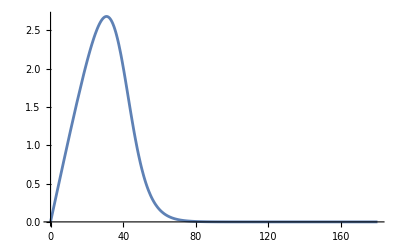

```mathematica
f[x_]:=(2*π*Sin[x*2π/360])/(1+E^((Abs[x*2π/360]-40*2π/360)/0.1))
Plot[f[x],{x,0,180}]
```

```mathematica
(* Make solver a function *)

(* Initial Conds & SOlver --- Need to redefine/recalculate forces INSIDE the functuon so that the vaired launch conditions are included in the force expressions *)
solveEquations[xo_,yo_,zo_,vxo_,vyo_,vzo_,αo_,ϕo_,ω_] := Module[{soln,disp,flighttime,zdisp},
Check[ (* Check is essentially a try-catch block, prevents a single error from stopping the entire remaining simulations *)
(* Force defns*)
V[t] = √(x'[t]^2+y'[t]^2+z'[t]^2); (* Velocity magnitude *)
L = 1/2 m*R^2*ω;
Subscript[α, crit] = 40*(2π/360);
Subscript[α, decay] = 0.1;
(* Angular momentum components in lab frame *)
Lx[t]=L*(x'[t]/V[t] Sin[α[t]]+y'[t]/V[t] Cos[α[t]]Cos[ϕ[t]]+z'[t]/V[t] Cos[α[t]]Sin[ϕ[t]]);
Ly[t]=L*(y'[t]/V[t] x'[t]/(√(x'[t]^2+z'[t]^2))Sin[α[t]]-(√(x'[t]^2+z'[t]^2))/V[t] Cos[α[t]]Cos[ϕ[t]]+y'[t]/V[t] z'[t]/(√(x'[t]^2+z'[t]^2))Cos[α[t]]Sin[ϕ[t]]);
Lz[t]=L*(z'[t]/(√(x'[t]^2+z'[t]^2))Sin[α[t]]-x'[t]/(√(x'[t]^2+z'[t]^2))Cos[α[t]]Sin[ϕ[t]]);
(*Lift components in lab frame - defined using the above ang mom components*)
(* Lift as function of v and l components*)
FLx[t]=(((π^2 R^2 ρ)/2 Sin[2α[t]] 1/(1+E^((Abs[α[t]]-Subscript[α, crit])/Subscript[α, decay])) (x'[t]^2+y'[t]^2+z'[t]^2) (Ly[t] x'[t] y'[t]+Lz[t] x'[t] z'[t]-Lx[t] (y'[t]^2+z'[t]^2)))/(√((x'[t]^2+y'[t]^2+z'[t]^2) (Lz[t]^2 (x'[t]^2+y'[t]^2)-2 Lx[t] Lz[t] x'[t] z'[t]-2 Ly[t] y'[t] (Lx[t] x'[t]+Lz[t] z'[t])+Ly[t]^2 (x'[t]^2+z'[t]^2)+Lx[t]^2 (y'[t]^2+z'[t]^2)))));
FLy[t]=-((π^2 R^2 ρ)/2 Sin[2α[t]] 1/(1+E^((Abs[α[t]]-Subscript[α, crit])/Subscript[α, decay])) (x'[t]^2+y'[t]^2+z'[t]^2) (-y'[t] (Lx[t] x'[t]+Lz[t] z'[t])+Ly[t] (x'[t]^2+z'[t]^2)))/(√((x'[t]^2+y'[t]^2+z'[t]^2) (Lz[t]^2 (x'[t]^2+y'[t]^2)-2 Lx[t] Lz[t] x'[t] z'[t]-2 Ly[t] y'[t] (Lx[t] x'[t]+Lz[t] z'[t])+Ly[t]^2 (x'[t]^2+z'[t]^2)+Lx[t]^2 (y'[t]^2+z'[t]^2))));
FLz[t]=-((π^2 R^2 ρ)/2 Sin[2α[t]] 1/(1+E^((Abs[α[t]]-Subscript[α, crit])/Subscript[α, decay]))(Lz[t] (x'[t]^2+y'[t]^2)-(Lx[t] x'[t]+Ly[t] y'[t]) z'[t]) (x'[t]^2+y'[t]^2+z'[t]^2))/(√((x'[t]^2+y'[t]^2+z'[t]^2) (Lz[t]^2 (x'[t]^2+y'[t]^2)-2 Lx[t] Lz[t] x'[t] z'[t]-2 Ly[t] y'[t] (Lx[t] x'[t]+Lz[t] z'[t])+Ly[t]^2 (x'[t]^2+z'[t]^2)+Lx[t]^2 (y'[t]^2+z'[t]^2))));



(* Drag force componenss. Using the experimentally determined value of CD for Ruellia seeds *)
(* Experimental drag expression based on measured Cd for R ciliatiflora *)
Subscript[C, D] = 0.301; (*5% uncertainity interval: (.259, .343) *)
Dx[t] = -(((Subscript[C, D]+(π^2*Abs[Sin[α[t]]]^2)/e(1/(1+E^((Abs[α[t]]-Subscript[α, crit])/Subscript[α, decay])))^2)*ρ)/2 V[t]*x'[t](π*R^2 Abs[Sin[α[t]]]+2d*R*Abs[Cos[α[t]]]));
Dy[t] = -(((Subscript[C, D]+(π^2*Abs[Sin[α[t]]]^2)/e(1/(1+E^((Abs[α[t]]-Subscript[α, crit])/Subscript[α, decay])))^2)*ρ)/2 V[t]*y'[t](π*R^2 Abs[Sin[α[t]]]+2d*R*Abs[Cos[α[t]]]));
Dz[t] = -(((Subscript[C, D]+(π^2*Abs[Sin[α[t]]]^2)/e(1/(1+E^((Abs[α[t]]-Subscript[α, crit])/Subscript[α, decay])))^2)*ρ)/2 V[t]*z'[t](π*R^2 Abs[Sin[α[t]]]+2d*R*Abs[Cos[α[t]]]));


(* Experimental magnus exrpression based on measured Cm for R ciliatiflora *)
Subscript[C, M]=0.0351;(*5% uncertainity interval: (.018, .052) *)
Mx[t] =-1/2 Subscript[C, M] ρ(d*2R)V[t](y'[t](Sin[α[t]]*z'[t]/(√(x'[t]^2+z'[t]^2))-Cos[α[t]]Sin[ϕ[t]]*x'[t]/(√(x'[t]^2+z'[t]^2)))-z'[t](y'[t]/V[t] x'[t]/(√(x'[t]^2+z'[t]^2))Sin[α[t]]-(√(x'[t]^2+z'[t]^2))/V[t] Cos[α[t]]Cos[ϕ[t]]+y'[t]/V[t] z'[t]/(√(x'[t]^2+z'[t]^2))Cos[α[t]]Sin[ϕ[t]]));
My[t] = -1/2 Subscript[C, M] ρ(d*2R)V[t](z'[t](Sin[α[t]]*x'[t]/V[t]+Cos[α[t]]Cos[ϕ[t]]*y'[t]/V[t]+Cos[α[t]]Sin[ϕ[t]]*z'[t]/V[t])-x'[t](Sin[α[t]]*z'[t]/(√(x'[t]^2+z'[t]^2))-Cos[α[t]]Sin[ϕ[t]]*x'[t]/(√(x'[t]^2+z'[t]^2))));
Mz[t] =-1/2 Subscript[C, M] ρ(d*2R)V[t](x'[t](y'[t]/V[t] x'[t]/(√(x'[t]^2+z'[t]^2))Sin[α[t]]-(√(x'[t]^2+z'[t]^2))/V[t] Cos[α[t]]Cos[ϕ[t]]+y'[t]/V[t] z'[t]/(√(x'[t]^2+z'[t]^2))Cos[α[t]]Sin[ϕ[t]])-y'[t](Sin[α[t]]*x'[t]/V[t]+Cos[α[t]]Cos[ϕ[t]]*y'[t]/V[t]+Cos[α[t]]Sin[ϕ[t]]*z'[t]/V[t]));
Subscript[eq, α] = α'[t] == (g *√(x'[t]^2+z'[t]^2))/V[t]^2 Cos[ϕ[t]]-(ρ*V[t]*π^2*R^2)/(2m)Sin[2α[t]] 1/(1+E^((Abs[α[t]]-Subscript[α, crit])/Subscript[α, decay]));
Subscript[eq, ϕ] = ϕ'[t] == -(π^3*R^3 ρ*V[t]^2)/(16*L)Sin[2*α[t]] 1/(1+E^((Abs[α[t]]-Subscript[α, crit])/Subscript[α, decay]));
Subscript[eq, x] = x''[t]==1/m(FLx[t]+Dx[t]+Mx[t]);
Subscript[eq, y] = y''[t]== 1/m(FLy[t]+Dy[t]+My[t])-g;
Subscript[eq, z] = z''[t] ==1/m(FLz[t]+Dz[t]+Mz[t]);
soln = NDSolve[{

(* 5 ODES *)
 Subscript[eq, α],Subscript[eq, ϕ], Subscript[eq, x], Subscript[eq, y],Subscript[eq, z], 
(* Initial conditions *)
ϕ[0]==ϕo,
α[0]==αo,
x[0]==xo,x'[0]==vxo,
y[0]==yo,y'[0]==vyo,
z[0]==zo,z'[0]==vzo},

{α,ϕ,x,y,z},{t,0,18}]  ;

(* get time disc hits ground, total displacement *)
flighttime = Part[FindRoot[0==y[t]/.soln,{t,.01,18}, Method->"Brent"],1] //Last;
disp=√(x[flighttime]^2+z[flighttime]^2)/.soln;
zdisp=z[flighttime]/.soln;
Return[{ϕo*(360/(2π)),αo*(360/(2π)),ArcTan[vyo/vxo]*(360/(2π)),ω,flighttime,Part[disp,1],Part[zdisp,1],soln}],
Print[{"Error:",ϕo*(360/(2π)),ArcTan[vyo/vxo]*(360/(2π)),ω}]; (* Error catching -- return the simulated conditions so you know where stuff is breaking *)
Return[{ϕo*(360/(2π)),αo*(360/(2π)),ArcTan[vyo/vxo]*(360/(2π)),ω,-1,-1,-1,-1}]]]
```

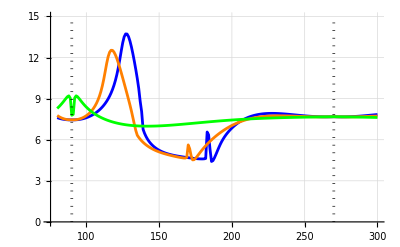

```mathematica
(*Initial betas 95% interval (38,42) *)
(*Phi ~270 (backspin), but not really possible to measure precisely *)
(*Initial velocities 95% interval (9.00, 10.63)*)
angles = Range[80*((2*π)/360),300*((2*π)/360),1*((2*π)/360)];
Subscript[x, o]=0;
Subscript[y, o]=1;
Subscript[z, o]=0;
Subscript[α, o]=(.1)*((2*π)/360);
Subscript[vx, o]=10*Cos[40*((2*π)/360)]; 
Subscript[vy, o]=10*Sin[40*((2*π)/360)];
Subscript[vz, o]=0; 

(* Quick check on dispersion range as function of phi for 3 different omegas. runs quickly & can be used to make sure everything is working properly.*)

(* General form for running a set of simulations using the Table command. Passes in each element of the list "angles" to the solver, solves the equations using the above initial conditions and the given phi value. *)
resultsTable = Table[solveEquations[Subscript[x, o],Subscript[y, o],Subscript[z, o],Subscript[vx, o],Subscript[vy, o],Subscript[vz, o],Subscript[α, o],phi,1660*2π],{phi,angles}];
resultsTableMid = Table[solveEquations[Subscript[x, o],Subscript[y, o],Subscript[z, o],Subscript[vx, o],Subscript[vy, o],Subscript[vz, o],Subscript[α, o],phi,1000*2π],{phi,angles}];
resultsTableLow = Table[solveEquations[Subscript[x, o],Subscript[y, o],Subscript[z, o],Subscript[vx, o],Subscript[vy, o],Subscript[vz, o],Subscript[α, o],phi,200*2π],{phi,angles}];

(* For the vertical lines denoting top & backspin*)
topspin = Transpose@{{90,90},{0,15}};
backspin = Transpose@{{270,270},{0,15}};


datadisp = Transpose@{resultsTable[[All,1]],resultsTable[[All,6]]};
datadispMid = Transpose@{resultsTableMid[[All,1]],resultsTableMid[[All,6]]};
datadispLow = Transpose@{resultsTableLow[[All,1]],resultsTableLow[[All,6]]};

ListLinePlot[{datadisp,datadispMid,datadispLow, topspin,backspin},
PlotStyle->{{Blue},{Orange}, {Green},{Black,Dotted},{Black,Dotted}},
PlotRange->All, GridLines->Automatic]
```

```mathematica
angles = Range[90*((2*π)/360),270*((2*π)/360),1*((2*π)/360)];
Subscript[x, o]=0;
Subscript[y, o]=0.5;
Subscript[z, o]=0;
Subscript[α, o]=(.1)*((2*π)/360);
beta1 = 40;
Subscript[vx, o]=10*Cos[beta1*((2*π)/360)]; 
Subscript[vy, o]=10*Sin[beta1*((2*π)/360)];
Subscript[vz, o]=0; 
omega1 = 1000;
ω=omega1*2π;
resultsTablePhi = Table[solveEquations[Subscript[x, o],Subscript[y, o],Subscript[z, o],Subscript[vx, o],Subscript[vy, o],Subscript[vz, o],Subscript[α, o],phi,ω],{phi,angles}];
```

```mathematica
plotListXYZ = {};
plotListXY = {};
plotListXZ = {};
plotListCoords = {};

xcoords = {};
zcoords = {};
colorcoords = {};
dists = {};

For[p=1, p<= Length[angles], p++,
Print[{resultsTablePhi[[p,1]],resultsTablePhi[[p,5]],resultsTablePhi[[p,6]],resultsTablePhi[[p,7]]}];
tland=resultsTablePhi[[p,5]];
soln=resultsTablePhi[[p,8]];
x[t]=soln{3};
y[t]=soln{4};
z[t]=soln{5};

xland = x[tland]/.soln;
zland = z[tland]/.soln;
AppendTo[dists,resultsTablePhi[[p,6]]];

AppendTo[xcoords,xland];
AppendTo[zcoords,zland];
AppendTo[colorcoords,p];
(*
plotXYZ = ParametricPlot3D[{x[t],y[t],z[t]}/.soln,{t,0,tland*1},
PlotRange->{{0,15},{0,5},{-7.5,7.5}}, 
PlotLabel->"3D trajectory ",
AxesLabel->{"x (m)","y (m)", "z (m)"},
PlotLegends->{resultsTablePhi[[p,1]]},
PlotStyle->{ColorData["Rainbow",p/Length[angles]]},
FaceGrids->{{1,0,0},{0,-1,0},{0,0,-1}},
ViewAngle->0.36449712460058503,ViewCenter->{0.5,0.5,0.5},
ViewMatrix->Automatic,ViewPoint->{-1.205461023704569,3.136085324249023,0.40228417736599875},
ViewProjection->Automatic,
ViewRange->All,
ViewVector->Automatic,
ViewVertical->{0.12734601200290835,0.9914635570294913,-0.027982285635446663}];

plotXY = ParametricPlot[{{x[t],y[t]}/.soln},{t,0,tland*1.1},
PlotRange->{{0,15},{0,15}}, 
PlotStyle->{ColorData["Rainbow",p/Length[angles]]},
PlotLabel->"Projected Trajectory XY Plane (vertical 'camera' plane) ",
AxesLabel->{"x (m)", "y (m)"},
PlotLegends->{resultsTablePhi[[p,1]]}];

plotXZ = ParametricPlot[{{x[t],z[t]}/.soln},{t,0,tland},
PlotRange->{{0,15},{-7.5,7.5}}, 
PlotStyle->{ColorData["Rainbow",p/Length[angles]]},
PlotLabel->"Projected Trajectory XZ Plane (Bird's eye view)",
AxesLabel->{"x (m)", "z (m)"},
PlotLegends->{resultsTablePhi[[p,1]]}];*)

plotLandCoords = ParametricPlot[{{x[t],z[t]}/.soln},{t,tland,tland+0.001},
PlotRange->{{0,15},{-12,12}}, 
PlotStyle->{ColorData["Rainbow",p/Length[angles]], Thickness[0.02]},
PlotLabel->"Landing Locations",
AxesLabel->{"x (m)", "z (m)"}
(*,PlotLegends->{resultsTablePhi[[p,1]]}*)];


AppendTo[plotListXYZ,plotXYZ];
AppendTo[plotListXY,plotXY];
AppendTo[plotListXZ,plotXZ];
AppendTo[plotListCoords, plotLandCoords];


xsol = x/. First[soln];
ysol = y/. First[soln];
zsol = z/. First[soln];
ϕsol = ϕ/. First[soln];
αsol = α/. First[soln];
trajData = {};
(*temp = Table[{t,xsol[t], ysol[t], zsol[t], ϕsol[t], αsol[t]},{t,0,10,.01}];

Export["C:\\Users\\hesse\\Desktop\\F21\\Thesis\\SimData\\SeedTrajectoryPhi_"<>ToString[N[angles[[p]]*(360/(2π))]]<>"csv",temp
];*)
]

(*XYZ=Show[plotListXYZ]
Export["C:\\Users\\hesse\\Desktop\\F21\\Thesis\\figures\\Results\\simple\\seed\\sd_combinedXYZ.jpg",XYZ];
XY=Show[plotListXY]
Export["C:\\Users\\hesse\\Desktop\\F21\\Thesis\\figures\\Results\\simple\\seed\\sd_combinedXY.jpg",XY];
XZ=Show[plotListXZ]
Export["C:\\Users\\hesse\\Desktop\\F21\\Thesis\\figures\\Results\\simple\\seed\\sd_combinedXZ.jpg",XZ];*)
(*coords = Show[plotListCoords]
Export["C:\\Users\\hesse\\Desktop\\F21\\Thesis\\figures\\Results\\simple\\seed\\sd_combined_landing" <> ToString[omega1]<>".jpg",coords];*)
(*
plotLandCoords = ListPlot[{xcoords,zcoords},
PlotRange->{{0,15},{-7.5,7.5}}, 
PlotStyle->{ColorData["Rainbow",colorcoords]},
PlotLabel->"Landing Coords",
AxesLabel->{"x (m)", "z (m)"},
PlotLegends->{resultsTablePhi[[p,1]]}
]
*)
```

{90,1.22211,7.11109,0.0299533}

{91,1.22264,7.1093,-0.115364}

{92,1.22455,7.11225,-0.260926}

{93,1.22786,7.12111,-0.407271}

{94,1.23261,7.13602,-0.554954}

{95,1.23885,7.15713,-0.704555}

{96,1.24662,7.18469,-0.856686}

{97,1.25603,7.21903,-1.012}

{98,1.26715,7.26055,-1.17122}

{99,1.28013,7.30978,-1.33514}

{100,1.2951,7.36739,-1.50463}

{101,1.31228,7.4342,-1.6807}

{102,1.33188,7.51127,-1.86453}

{103,1.35421,7.59995,-2.05746}

{104,1.37963,7.70195,-2.26112}

{105,1.40862,7.81949,-2.47741}

{106,1.44179,7.95551,-2.70868}

{107,1.47993,8.11387,-2.95778}

{108,1.5241,8.29983,-3.22818}

{109,1.5757,8.52058,-3.52406}

{110,1.63669,8.78592,-3.85011}

{111,1.70964,9.10901,-4.2107}

{112,1.79785,9.50577,-4.60674}

{113,1.90451,9.98894,-5.02692}

{114,2.02983,10.5473,-5.42995}

{115,2.16567,11.1126,-5.73438}

{116,2.29626,11.5732,-5.86347}

{117,2.40943,11.8576,-5.80961}

{118,2.50221,11.9656,-5.61824}

{119,2.57668,11.9302,-5.33969}

{120,2.636,11.7877,-5.01057}

{121,2.683,11.5674,-4.65434}

{122,2.71993,11.292,-4.28551}

{123,2.74857,10.9781,-3.91304}

{124,2.77031,10.6381,-3.54241}

{125,2.7863,10.2811,-3.17694}

{126,2.79751,9.91349,-2.81861}

{127,2.80482,9.5392,-2.46852}

{128,2.80909,9.15965,-2.12739}

{129,2.81135,8.77337,-1.79615}

{130,2.81306,8.37495,-1.4772}

{131,2.81717,7.95315,-1.17812}

{132,2.83159,7.4915,-0.926201}

{133,2.88494,7.02951,-0.826472}

{134,2.68433,6.63062,-2.33642}

{135,2.58919,6.30867,-2.40586}

{136,2.53929,6.15332,-2.36062}

{137,2.50212,6.01982,-2.29245}

{138,2.47217,5.90088,-2.21558}

{139,2.44667,5.7941,-2.13512}

{140,2.42445,5.69782,-2.05325}

{141,2.40483,5.61066,-1.97097}

{142,2.38737,5.53151,-1.88864}

{143,2.37177,5.45938,-1.8064}

{144,2.35777,5.39346,-1.72418}

{145,2.34519,5.33305,-1.64185}

{146,2.33388,5.27755,-1.55926}

{147,2.32372,5.2264,-1.47621}

{148,2.31461,5.17915,-1.39253}

{149,2.30647,5.13538,-1.30804}

{150,2.29924,5.09469,-1.2226}

{151,2.29285,5.05674,-1.13607}

{152,2.28727,5.02122,-1.04836}

{153,2.28245,4.98782,-0.959423}

{154,2.27836,4.9563,-0.869235}

{155,2.27497,4.9264,-0.777821}

{156,2.27226,4.89792,-0.685245}

{157,2.2702,4.87069,-0.591612}

{158,2.26876,4.84455,-0.497053}

{159,2.26792,4.81941,-0.401712}

{160,2.26767,4.79518,-0.305738}

{161,2.26801,4.77184,-0.209271}

{162,2.26895,4.7494,-0.112428}

{163,2.27054,4.72792,-0.0152925}

{164,2.27292,4.70752,0.082092}

{165,2.27634,4.68847,0.179695}

{166,2.28143,4.67131,0.277407}

{167,2.29016,4.65758,0.37475}

{168,2.30357,4.65289,0.469668}

{169,2.32395,4.69646,0.541807}

{170,2.47314,5.50103,2.29445}

{171,2.42113,5.23889,2.46252}

{172,2.36879,4.7647,2.62515}

{173,2.32713,4.51954,2.61532}

{174,2.29984,4.53301,2.72244}

{175,2.27934,4.62304,2.86819}

{176,2.26166,4.73947,3.01519}

{177,2.24521,4.86488,3.15229}

{178,2.22928,4.99105,3.27601}

{179,2.21358,5.11383,3.38627}

{180,2.198,5.23174,3.48471}

{181,2.18251,5.34476,3.57322}

{182,2.1671,5.45323,3.65324}

{183,2.15174,5.55751,3.72578}

{184,2.13642,5.6579,3.79156}

{185,2.12113,5.75462,3.85114}

{186,2.10588,5.84786,3.90492}

{187,2.09065,5.93776,3.95322}

{188,2.07544,6.02441,3.99632}

{189,2.06026,6.10792,4.03441}

{190,2.04509,6.18834,4.0677}

{191,2.02995,6.26575,4.09634}

{192,2.01483,6.3402,4.12048}

{193,1.99975,6.41173,4.14026}

{194,1.98469,6.48038,4.1558}

{195,1.96967,6.5462,4.16722}

{196,1.95469,6.60922,4.17463}

{197,1.93975,6.66948,4.17815}

{198,1.92486,6.72704,4.17789}

{199,1.91002,6.78191,4.17395}

{200,1.89524,6.83416,4.16645}

{201,1.88053,6.88381,4.15548}

{202,1.86589,6.93092,4.14117}

{203,1.85132,6.97554,4.12362}

{204,1.83683,7.01771,4.10294}

{205,1.82243,7.05748,4.07923}

{206,1.80813,7.09491,4.05261}

{207,1.79392,7.13005,4.02318}

{208,1.77982,7.16297,3.99106}

{209,1.76583,7.1937,3.95634}

{210,1.75196,7.22232,3.91914}

{211,1.73821,7.24889,3.87957}

{212,1.72459,7.27347,3.83772}

{213,1.7111,7.29611,3.79371}

{214,1.69776,7.31689,3.74764}

{215,1.68456,7.33588,3.69962}

{216,1.67152,7.35312,3.64973}

{217,1.65863,7.3687,3.59809}

{218,1.64591,7.38268,3.54478}

{219,1.63336,7.39513,3.4899}

{220,1.62099,7.4061,3.43356}

{221,1.60879,7.41568,3.37583}

{222,1.59678,7.42393,3.3168}

{223,1.58496,7.43091,3.25656}

{224,1.57333,7.43669,3.1952}

{225,1.5619,7.44133,3.13279}

{226,1.55068,7.44491,3.06941}

{227,1.53966,7.44749,3.00513}

{228,1.52886,7.44913,2.94003}

{229,1.51828,7.4499,2.87417}

{230,1.50791,7.44986,2.80763}

{231,1.49777,7.44906,2.74045}

{232,1.48785,7.44758,2.67271}

{233,1.47817,7.44547,2.60446}

{234,1.46872,7.44278,2.53575}

{235,1.4595,7.43959,2.46663}

{236,1.45053,7.43593,2.39715}

{237,1.44179,7.43187,2.32735}

{238,1.43331,7.42746,2.25728}

{239,1.42507,7.42274,2.18697}

{240,1.41708,7.41778,2.11646}

{241,1.40934,7.41262,2.04579}

{242,1.40185,7.4073,1.97497}

{243,1.39462,7.40187,1.90405}

{244,1.38765,7.39638,1.83304}

{245,1.38093,7.39086,1.76197}

{246,1.37448,7.38537,1.69086}

{247,1.36828,7.37993,1.61972}

{248,1.36235,7.37458,1.54858}

{249,1.35669,7.36936,1.47744}

{250,1.35129,7.36431,1.40632}

{251,1.34615,7.35946,1.33522}

{252,1.34128,7.35483,1.26415}

{253,1.33668,7.35046,1.19313}

{254,1.33235,7.34638,1.12215}

{255,1.32828,7.34261,1.05121}

{256,1.32449,7.33917,0.980317}

{257,1.32096,7.3361,0.90947}

{258,1.31771,7.3334,0.838667}

{259,1.31472,7.33111,0.767904}

{260,1.31201,7.32924,0.697178}

{261,1.30957,7.3278,0.626481}

{262,1.3074,7.32681,0.55581}

{263,1.30551,7.32629,0.485155}

{264,1.30388,7.32624,0.414509}

{265,1.30253,7.32668,0.343864}

{266,1.30145,7.32761,0.273211}

{267,1.30064,7.32904,0.202539}

{268,1.3001,7.33096,0.131838}

{269,1.29984,7.33336,0.0610993}

{270,1.29983,7.33619,-0.00968813}

```mathematica
Export["C:\\Users\\hesse\\Desktop\\temp.csv",dists]
```

C:\Users\hesse\Desktop\temp.csv

```mathematica
{temp[[1,;;]],temp[[2,;;]]}
temp[[;;,;;]]
```

{{0.,0.,0.5,0.,4.71239,0.00174533},{0.1,0.739416,1.07705,-0.0014857,4.71077,-0.00001462}}

{{0.,0.,0.5,0.,4.71239,0.00174533},{0.1,0.739416,1.07705,-0.0014857,4.71077,-0.00001462},{0.2,1.43242,1.53011,-0.00292243,4.71089,-0.0000183086},{0.3,2.08726,1.8682,-0.00417165,4.71102,-0.0000222637},{0.4,2.71023,2.09819,-0.00525061,4.71113,-0.0000260004},{0.5,3.30604,2.2254,-0.00617445,4.71125,-0.0000286167},{0.6,3.87811,2.25408,-0.00695741,4.71135,-0.0000291462},{0.7,4.42885,2.18787,-0.00761371,4.71145,-0.0000271463},{0.8,4.95978,2.03014,-0.00815801,4.71154,-0.0000231862},{0.9,5.4718,1.7843,-0.00860516,4.71161,-0.0000184665},{1.,5.96536,1.45405,-0.00896952,4.71167,-0.0000140528},{1.1,6.44067,1.04342,-0.00926418,4.71173,-0.0000104673},{1.2,6.89782,0.556829,-0.00950058,4.71177,-7.76805×10^-6},{1.3,7.3369,-0.000988435,-0.00968841,4.71181,-5.82088×10^-6},{1.4,7.75808,-0.625063,-0.00983573,4.71184,-4.42708×10^-6},{1.5,8.16165,-1.3103,-0.00994928,4.71187,-3.42903×10^-6},{1.6,8.54798,-2.05161,-0.0100347,4.71189,-2.7083×10^-6},{1.7,8.9176,-2.84395,-0.0100967,4.71191,-2.17863×10^-6},{1.8,9.27112,-3.68247,-0.0101392,4.71193,-1.78667×10^-6},{1.9,9.60923,-4.56255,-0.0101656,4.71195,-1.48919×10^-6},{2.,9.93267,-5.47983,-0.0101787,4.71196,-1.26053×10^-6},{2.1,10.2422,-6.43028,-0.010181,4.71198,-1.08401×10^-6},{2.2,10.5388,-7.41018,-0.0101744,4.71199,-9.40842×10^-7},{2.3,10.823,-8.41613,-0.0101608,4.712,-8.27932×10^-7},{2.4,11.0959,-9.44508,-0.0101415,4.71201,-7.3504×10^-7},{2.5,11.3581,-10.4943,-0.0101179,4.71202,-6.60501×10^-7},{2.6,11.6105,-11.5612,-0.0100909,4.71202,-5.9725×10^-7},{2.7,11.8537,-12.6437,-0.0100615,4.71203,-5.45483×10^-7},{2.8,12.0884,-13.7398,-0.0100303,4.71204,-5.01744×10^-7},{2.9,12.3153,-14.8479,-0.00999793,4.71205,-4.63647×10^-7},{3.,12.5351,-15.9663,-0.00996496,4.71205,-4.31066×10^-7},{3.1,12.7482,-17.0939,-0.00993176,4.71206,-4.03197×10^-7},{3.2,12.9552,-18.2293,-0.00989867,4.71207,-3.78981×10^-7},{3.3,13.1567,-19.3717,-0.00986596,4.71207,-3.5738×10^-7},{3.4,13.353,-20.52,-0.00983383,4.71208,-3.37807×10^-7},{3.5,13.5445,-21.6736,-0.00980247,4.71208,-3.21895×10^-7},{3.6,13.7318,-22.8318,-0.009772,4.71209,-3.06916×10^-7},{3.7,13.915,-23.9939,-0.00974252,4.71209,-2.92276×10^-7},{3.8,14.0946,-25.1596,-0.00971409,4.71209,-2.83266×10^-7},{3.9,14.2709,-26.3283,-0.00968678,4.7121,-2.70659×10^-7},{4.,14.4441,-27.4996,-0.00966061,4.7121,-2.61804×10^-7},{4.1,14.6145,-28.6732,-0.00963558,4.71211,-2.52491×10^-7},{4.2,14.7823,-29.8489,-0.00961172,4.71211,-2.44387×10^-7},{4.3,14.9477,-31.0263,-0.009589,4.71211,-2.36953×10^-7},{4.4,15.111,-32.2053,-0.0095674,4.71212,-2.3014×10^-7},{4.5,15.2723,-33.3856,-0.00954692,4.71212,-2.2382×10^-7},{4.6,15.4317,-34.5671,-0.00952751,4.71213,-2.17987×10^-7},{4.7,15.5895,-35.7497,-0.00950915,4.71213,-2.12566×10^-7},{4.8,15.7457,-36.9332,-0.00949179,4.71213,-2.07513×10^-7},{4.9,15.9005,-38.1175,-0.00947541,4.71214,-2.02795×10^-7},{5.,16.054,-39.3026,-0.00945996,4.71214,-1.98371×10^-7},{5.1,16.2063,-40.4882,-0.00944541,4.71214,-1.94214×10^-7},{5.2,16.3576,-41.6744,-0.00943171,4.71214,-1.90298×10^-7},{5.3,16.5078,-42.8611,-0.00941883,4.71215,-1.86597×10^-7},{5.4,16.6571,-44.0483,-0.00940672,4.71215,-1.83092×10^-7},{5.5,16.8056,-45.2358,-0.00939535,4.71215,-1.79764×10^-7},{5.6,16.9533,-46.4237,-0.00938467,4.71216,-1.76597×10^-7},{5.7,17.1003,-47.6119,-0.00937466,4.71216,-1.73577×10^-7},{5.8,17.2466,-48.8003,-0.00936527,4.71216,-1.70689×10^-7},{5.9,17.3923,-49.989,-0.00935648,4.71216,-1.67924×10^-7},{6.,17.5375,-51.178,-0.00934825,4.71217,-1.65269×10^-7},{6.1,17.6821,-52.3671,-0.00934054,4.71217,-1.62719×10^-7},{6.2,17.8263,-53.5564,-0.00933333,4.71217,-1.6026×10^-7},{6.3,17.9701,-54.7458,-0.00932658,4.71218,-1.57888×10^-7},{6.4,18.1134,-55.9354,-0.00932028,4.71218,-1.55599×10^-7},{6.5,18.2564,-57.1251,-0.00931439,4.71218,-1.53375×10^-7},{6.6,18.3991,-58.3149,-0.00930888,4.71218,-1.51237×10^-7},{6.7,18.5415,-59.5048,-0.00930375,4.71218,-1.49136×10^-7},{6.8,18.6836,-60.6948,-0.00929895,4.71219,-1.47112×10^-7},{6.9,18.8254,-61.8849,-0.00929447,4.71219,-1.45156×10^-7},{7.,18.967,-63.0751,-0.00929029,4.71219,-1.43085×10^-7},{7.1,19.1084,-64.2653,-0.0092864,4.71219,-1.41488×10^-7},{7.2,19.2495,-65.4556,-0.00928277,4.7122,-1.39623×10^-7},{7.3,19.3905,-66.646,-0.00927938,4.7122,-1.36731×10^-7},{7.4,19.5313,-67.8364,-0.00927623,4.7122,-1.36429×10^-7},{7.5,19.672,-69.0268,-0.00927329,4.7122,-1.34312×10^-7},{7.6,19.8125,-70.2173,-0.00927055,4.71221,-1.32647×10^-7},{7.7,19.9529,-71.4078,-0.009268,4.71221,-1.30955×10^-7},{7.8,20.0932,-72.5984,-0.00926562,4.71221,-1.29343×10^-7},{7.9,20.2333,-73.789,-0.00926341,4.71221,-1.27762×10^-7},{8.,20.3734,-74.9796,-0.00926135,4.71221,-1.26215×10^-7},{8.1,20.5133,-76.1702,-0.00925943,4.71222,-1.2469×10^-7},{8.2,20.6532,-77.3609,-0.00925765,4.71222,-1.23191×10^-7},{8.3,20.793,-78.5516,-0.00925599,4.71222,-1.21718×10^-7},{8.4,20.9327,-79.7423,-0.00925445,4.71222,-1.20268×10^-7},{8.5,21.0723,-80.933,-0.00925301,4.71222,-1.18843×10^-7},{8.6,21.2119,-82.1238,-0.00925168,4.71223,-1.17439×10^-7},{8.7,21.3515,-83.3145,-0.00925043,4.71223,-1.16058×10^-7},{8.8,21.4909,-84.5053,-0.00924928,4.71223,-1.14694×10^-7},{8.9,21.6304,-85.6961,-0.0092482,4.71223,-1.13351×10^-7},{9.,21.7697,-86.8869,-0.0092472,4.71223,-1.12031×10^-7},{9.1,21.9091,-88.0777,-0.00924628,4.71223,-1.10727×10^-7},{9.2,22.0484,-89.2685,-0.00924541,4.71224,-1.0944×10^-7},{9.3,22.1877,-90.4593,-0.00924461,4.71224,-1.08172×10^-7},{9.4,22.3269,-91.6502,-0.00924386,4.71224,-1.06921×10^-7},{9.5,22.4661,-92.841,-0.00924317,4.71224,-1.05687×10^-7},{9.6,22.6053,-94.0318,-0.00924253,4.71224,-1.04468×10^-7},{9.7,22.7445,-95.2227,-0.00924193,4.71224,-1.03266×10^-7},{9.8,22.8836,-96.4136,-0.00924137,4.71225,-1.02079×10^-7},{9.9,23.0227,-97.6044,-0.00924085,4.71225,-1.00908×10^-7},{10.,23.1618,-98.7953,-0.00924037,4.71225,-9.9751×10^-8}}

```mathematica
(* Range of intiial coniditions to check*)
angles = Range[80*((2*π)/360),460*((2*π)/360),2*((2*π)/360)]; (* Launch angles for phi ϕ -- Symmetric about 270 *)
anglesBeta = Range[0*((2*π)/360),65*((2*π)/360),2.5*((2*π)/360)];
initialOmegas = 2π*Range[200,4000,100];
heights = Range[0.5,1.5,.125];
```

```mathematica
(* launch angles phi vs beta solver *)
Clear[Subscript[x, o],Subscript[y, o],Subscript[z, o],Subscript[α, o],Subscript[ϕ, o],Subscript[vx, o],Subscript[vy, o],Subscript[vz, o],Subscript[v, o],ω]
Subscript[x, o]=0;
Subscript[y, o]=1;
Subscript[z, o]=0;
Subscript[α, o]=(0.1)*((2*π)/360);
Subscript[ϕ, o]=270*((2*π)/360);
Subscript[vz, o]=0; 
Subscript[v, o]=10;
ω=500*2π;
L = .5*m*R^2*ω;
resultsTableBeta = Table[solveEquations[Subscript[x, o],Subscript[y, o],Subscript[z, o],Cos[beta]*Subscript[v, o],Sin[beta]*Subscript[v, o],Subscript[vz, o],Subscript[α, o],phi,ω],{phi,angles}, {beta,anglesBeta}];
resultsTableBeta2 = Table[solveEquations[Subscript[x, o],Subscript[y, o],Subscript[z, o],Cos[beta]*Subscript[v, o],Sin[beta]*Subscript[v, o],Subscript[vz, o],Subscript[α, o],phi,1000*2π],{phi,angles}, {beta,anglesBeta}];
resultsTableBeta3 = Table[solveEquations[Subscript[x, o],Subscript[y, o],Subscript[z, o],Cos[beta]*Subscript[v, o],Sin[beta]*Subscript[v, o],Subscript[vz, o],Subscript[α, o],phi,1500*2π],{phi,angles}, {beta,anglesBeta}];
```

Clear::ssym: x_o is not a symbol or a valid string pattern.

Clear::ssym: y_o is not a symbol or a valid string pattern.

Clear::ssym: z_o is not a symbol or a valid string pattern.

General::stop: Further output of Clear::ssym will be suppressed during this calculation.

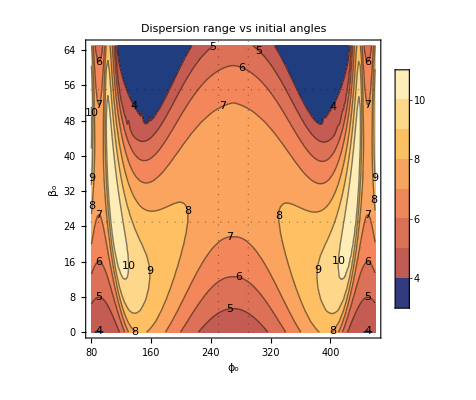

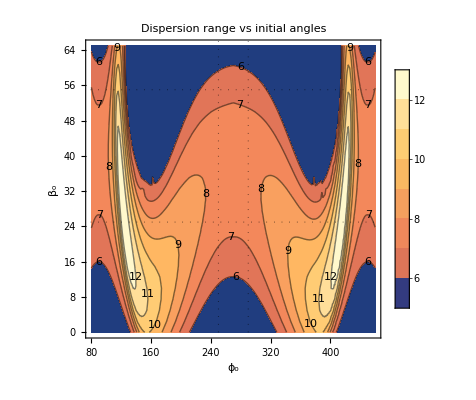

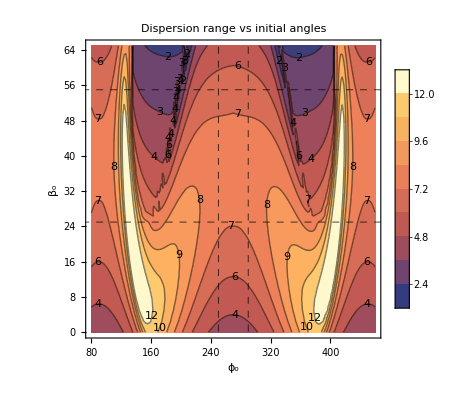

```mathematica
(* Contour plot the results of above sim block *)
dispList = {};
dispList2={};
dispList3={};
zdispList = {};
zdispList2={};
zdispList3={};
For[p=1, p<= Length[angles], p++,
For[b=1,b<=Length[anglesBeta],b++,
AppendTo[dispList,{angles[[p]]*(360/(2π)),anglesBeta[[b]]*(360/(2π)),resultsTableBeta[[p,b,6]]}];
AppendTo[dispList2,{angles[[p]]*(360/(2π)),anglesBeta[[b]]*(360/(2π)),resultsTableBeta2[[p,b,6]]}];
AppendTo[dispList3,{angles[[p]]*(360/(2π)),anglesBeta[[b]]*(360/(2π)),resultsTableBeta3[[p,b,6]]}];
AppendTo[zdispList,{angles[[p]]*(360/(2π)),anglesBeta[[b]]*(360/(2π)),resultsTableBeta[[p,b,7]]}];
AppendTo[zdispList2,{angles[[p]]*(360/(2π)),anglesBeta[[b]]*(360/(2π)),resultsTableBeta2[[p,b,7]]}];
AppendTo[zdispList3,{angles[[p]]*(360/(2π)),anglesBeta[[b]]*(360/(2π)),resultsTableBeta3[[p,b,7]]}];

]
]
(*Print[dispList]*)
contour = ListContourPlot[dispList,InterpolationOrder->1,Contours->Range[4,12,1], 
ContourLabels->True,
PlotLegends->Automatic,
FrameLabel->{"ϕ_o","β_o"},
GridLines-> {{250,290},{25,55}},
GridLinesStyle->Directive[Black,Thick,Dotted],
PlotLabel->"Dispersion range vs initial angles"];

contour2 = ListContourPlot[dispList2,InterpolationOrder->4,Contours->Range[6,12,1], 
ContourLabels->True,
PlotLegends->Automatic,
FrameLabel->{"ϕ_o","β_o"},
GridLines-> {{250,290},{25,55}},
GridLinesStyle->Directive[Black,Thick,Dotted],
PlotLabel->"Dispersion range vs initial angles"];

contour3 = ListContourPlot[dispList3,InterpolationOrder->1,Contours->10, 
ContourLabels->True,
PlotLegends->Automatic,
FrameLabel->{"ϕ_o","β_o"},
GridLines-> {{250,290},{25,55}},
GridLinesStyle->Directive[Black,Thick,Dashed],
PlotLabel->"Dispersion range vs initial angles"];

Show[contour]
Show[contour2]
Show[contour3]

(*(*Print[dispList]*)
zcontour = ListContourPlot[zdispList,InterpolationOrder->1,Contours->Range[0,5,.5], 
ContourLabels->True,
PlotLegends->Automatic,
FrameLabel->{"ϕ_o","β_o"},
GridLines-> {{265,275},{38,42}},
GridLinesStyle->Directive[Black,Thick],
PlotLabel->"Off-horiz range vs initial angles"];

zcontour2 = ListContourPlot[zdispList2,InterpolationOrder->1,Contours->Range[0,5,.5], 
ContourLabels->True,
PlotLegends->Automatic,
FrameLabel->{"ϕ_o","β_o"},
GridLines-> {{265,275},{38,42}},
GridLinesStyle->Directive[Black,Thick],
PlotLabel->"Off-horiz range vs initial angles"];

zcontour3 = ListContourPlot[zdispList3,InterpolationOrder->1,Contours->Range[0,5,.5], 
ContourLabels->True,
PlotLegends->Automatic,
FrameLabel->{"ϕ_o","β_o"},
GridLines-> {{265,275},{38,42}},
GridLinesStyle->Directive[Black,Thick],
PlotLabel->"Off-horiz range vs initial angles"];
Show[zcontour]
Show[zcontour2]
Show[zcontour3]*)
```

```mathematica
(* SPin rate contours *)
Clear[Subscript[x, o],Subscript[y, o],Subscript[z, o],Subscript[α, o],Subscript[ϕ, o],Subscript[vx, o],Subscript[vy, o],Subscript[vz, o],Subscript[v, o],ω]
Subscript[x, o]=0;
Subscript[y, o]=1;
Subscript[z, o]=0;
Subscript[α, o]=(0.1)*((2*π)/360);
Subscript[ϕ, o]=270*((2*π)/360);
Subscript[v, o]=10;
Subscript[vx, o] = Subscript[v, o]*Cos[40*((2π)/360)];
Subscript[vy, o] = Subscript[v, o]*Sin[40*((2π)/360)];
Subscript[vz, o]=0; 
ω=1600;
resultsTableOmega = Table[solveEquations[Subscript[x, o],Subscript[y, o],Subscript[z, o],Subscript[v, o]*Cos[30*((2π)/360)],Subscript[v, o]*Sin[30*((2π)/360)],Subscript[vz, o],Subscript[α, o],phi,omega],{phi,angles}, {omega,initialOmegas}];
resultsTableOmega2 = Table[solveEquations[Subscript[x, o],Subscript[y, o],Subscript[z, o],Subscript[v, o]*Cos[40*((2π)/360)],Subscript[v, o]*Sin[40*((2π)/360)],Subscript[vz, o],Subscript[α, o],phi,omega],{phi,angles}, {omega,initialOmegas}];
resultsTableOmega3 = Table[solveEquations[Subscript[x, o],Subscript[y, o],Subscript[z, o],Subscript[v, o]*Cos[50*((2π)/360)],Subscript[v, o]*Sin[50*((2π)/360)],Subscript[vz, o],Subscript[α, o],phi,omega],{phi,angles}, {omega,initialOmegas}];
```

Clear::ssym: x_o is not a symbol or a string.

Clear::ssym: y_o is not a symbol or a string.

Clear::ssym: z_o is not a symbol or a string.

General::stop: Further output of Clear::ssym will be suppressed during this calculation.

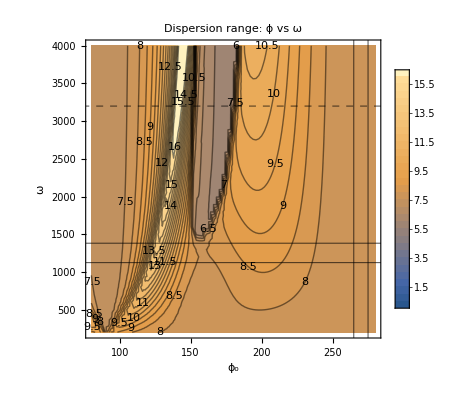

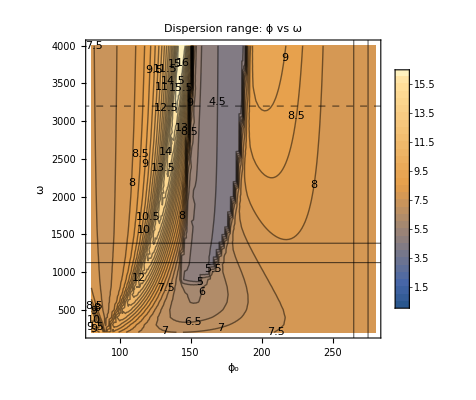

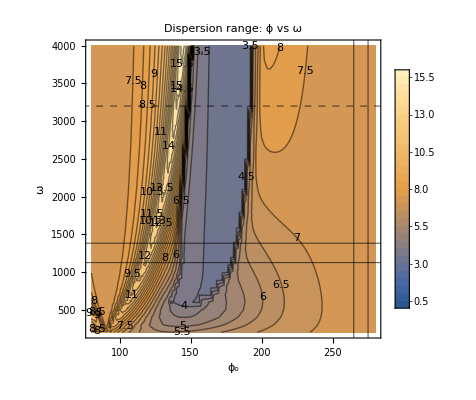

```mathematica
dispList = {};
dispList2 = {};
dispList3 = {};
zdispList = {};
For[p=1, p<= Length[angles], p++,
For[o=1,o<=Length[initialOmegas],o++,
AppendTo[dispList,{angles[[p]]*(360/(2π)),initialOmegas[[o]]/(2π),resultsTableOmega[[p,o,6]]}];
AppendTo[dispList2,{angles[[p]]*(360/(2π)),initialOmegas[[o]]/(2π),resultsTableOmega2[[p,o,6]]}];
AppendTo[dispList3,{angles[[p]]*(360/(2π)),initialOmegas[[o]]/(2π),resultsTableOmega3[[p,o,6]]}];


]
]
(*Print[dispList]*)
ListContourPlot[dispList,InterpolationOrder->1,Contours->Range[0,16,.5], 
ContourLabels->True,
PlotLegends->Automatic,
PlotRange->All,
FrameLabel->{"ϕ_o","ω"},
GridLines-> { {265,275},{1122,1382,{3200,Directive[Black,Dashed]}} },
GridLinesStyle->Directive[Black,Thick],
PlotLabel->"Dispersion range: ϕ vs ω"]

ListContourPlot[dispList2,InterpolationOrder->1,Contours->Range[0,16,.5], 
ContourLabels->True,
PlotLegends->Automatic,
PlotRange->All,
FrameLabel->{"ϕ_o","ω"},
GridLines-> { {265,275},{1122,1382,{3200,Directive[Black,Dashed]}} },
GridLinesStyle->Directive[Black,Thick],
PlotLabel->"Dispersion range: ϕ vs ω"]

ListContourPlot[dispList3,InterpolationOrder->1,Contours->Range[0,16,.5], 
ContourLabels->True,
PlotLegends->Automatic,
PlotRange->All,
FrameLabel->{"ϕ_o","ω"},
GridLines-> { {265,275},{1122,1382,{3200,Directive[Black,Dashed]}} },
GridLinesStyle->Directive[Black,Thick],
PlotLabel->"Dispersion range: ϕ vs ω"]
```

```mathematica
(* beta omega backspin*)
Clear[Subscript[x, o],Subscript[y, o],Subscript[z, o],Subscript[α, o],Subscript[ϕ, o],Subscript[vx, o],Subscript[vy, o],Subscript[vz, o],Subscript[v, o],ω]
Subscript[x, o]=0;
Subscript[y, o]=1;
Subscript[z, o]=0;
Subscript[v, o]=9.81;
Subscript[α, o]=(0.1)*((2*π)/360);
Subscript[ϕ, o]=270*((2*π)/360);
Subscript[vx, o] = Subscript[v, o]*Cos[40*((2π)/360)];
Subscript[vy, o] = Subscript[v, o]*Sin[40*((2π)/360)];
Subscript[vz, o]=0; 
ω=1600;
resultsTableBetaOmega= Table[solveEquations[Subscript[x, o],Subscript[y, o],Subscript[z, o],Cos[beta]*Subscript[v, o],Sin[beta]*Subscript[v, o],Subscript[vz, o],Subscript[α, o],Subscript[ϕ, o],omega],{omega,initialOmegas}, {beta,anglesBeta}];
```

Clear::ssym: x_o is not a symbol or a string.

Clear::ssym: y_o is not a symbol or a string.

Clear::ssym: z_o is not a symbol or a string.

General::stop: Further output of Clear::ssym will be suppressed during this calculation.

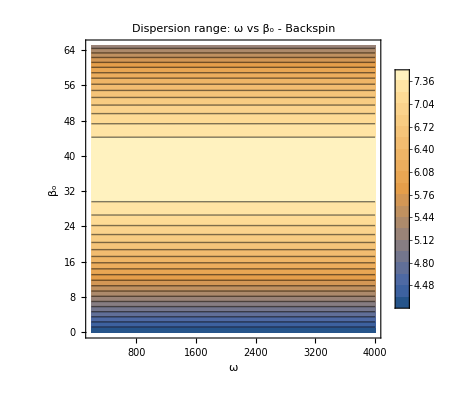

```mathematica
dispList = {};
zdispList = {};
For[o=1, o<= Length[initialOmegas], o++,
For[b=1,b<=Length[anglesBeta],b++,
AppendTo[dispList,{initialOmegas[[o]]/(2π),anglesBeta[[b]]*(360/(2π)),resultsTableBetaOmega[[o,b,6]]}];
AppendTo[zdispList,{initialOmegas[[o]]/(2π),anglesBeta[[b]]*(360/(2π)),resultsTableBetaOmega[[o,b,7]]}];

]
]
(*Print[dispList]*)
contour = ListContourPlot[dispList,InterpolationOrder->1,Contours->20, 
ContourLabels->Automatic,
PlotLegends->Automatic,
FrameLabel->{"ω","β_o"},
PlotLabel->"Dispersion range: ω vs β_o - Backspin"];

seedpoints = { {(√(5.51^2+4.63^2))/R,40.06},{(√(4.85^2+5.0^2))/R,45.89},{(√(3.23^2+3.15^2))/R,44.29},{(√(3.67^2+2.83^2))/R,37.61} }; (*from auditorium*)

Show[contour]
```

```mathematica
(* beta omega topspin*)
Clear[Subscript[x, o],Subscript[y, o],Subscript[z, o],Subscript[α, o],Subscript[ϕ, o],Subscript[vx, o],Subscript[vy, o],Subscript[vz, o],Subscript[v, o],ω]
Subscript[x, o]=0;
Subscript[y, o]=1;
Subscript[z, o]=0;
Subscript[α, o]=(0)*((2*π)/360);
Subscript[ϕ, o]=91*((2*π)/360);
Subscript[vx, o] = Subscript[v, o]*Cos[40*((2π)/360)];
Subscript[vy, o] = Subscript[v, o]*Sin[40*((2π)/360)];
Subscript[vz, o]=0; 
Subscript[v, o]=10;
ω=1600;
resultsTableBetaOmega= Table[solveEquations[Subscript[x, o],Subscript[y, o],Subscript[z, o],Cos[beta]*Subscript[v, o],Sin[beta]*Subscript[v, o],Subscript[vz, o],Subscript[α, o],Subscript[ϕ, o],omega],{omega,initialOmegas}, {beta,anglesBeta}];
```

Clear::ssym: x_o is not a symbol or a string.

Clear::ssym: y_o is not a symbol or a string.

Clear::ssym: z_o is not a symbol or a string.

General::stop: Further output of Clear::ssym will be suppressed during this calculation.

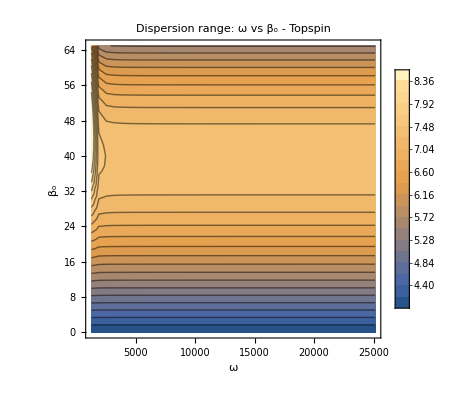

```mathematica
dispList = {};
zdispList = {};
For[o=1, o<= Length[initialOmegas], o++,
For[b=1,b<=Length[anglesBeta],b++,
AppendTo[dispList,{initialOmegas[[o]],anglesBeta[[b]]*(360/(2π)),resultsTableBetaOmega[[o,b,6]]}];
AppendTo[zdispList,{initialOmegas[[o]],anglesBeta[[b]]*(360/(2π)),resultsTableBetaOmega[[o,b,7]]}];

]
]
(*Print[dispList]*)
ListContourPlot[dispList,InterpolationOrder->1,Contours->20, 
ContourLabels->Automatic,
PlotLegends->Automatic,
FrameLabel->{"ω","β_o"},
PlotLabel->"Dispersion range: ω vs β_o - Topspin"]
```

```mathematica
(* beta omega sidespin*)
Clear[Subscript[x, o],Subscript[y, o],Subscript[z, o],Subscript[α, o],Subscript[ϕ, o],Subscript[vx, o],Subscript[vy, o],Subscript[vz, o],Subscript[v, o],ω]
Subscript[x, o]=0;
Subscript[y, o]=1;
Subscript[z, o]=0;
Subscript[α, o]=(0.1)*((2*π)/360);
Subscript[ϕ, o]=180*((2*π)/360);
Subscript[vx, o] = Subscript[v, o]*Cos[45*((2π)/360)];
Subscript[vy, o] = Subscript[v, o]*Sin[45*((2π)/360)];
Subscript[vz, o]=0; 
Subscript[v, o]=10;
ω=1600;
resultsTableBetaOmega= Table[solveEquations[Subscript[x, o],Subscript[y, o],Subscript[z, o],Cos[beta]*Subscript[v, o],Sin[beta]*Subscript[v, o],Subscript[vz, o],Subscript[α, o],Subscript[ϕ, o],omega],{omega,initialOmegas}, {beta,anglesBeta}];
```

Clear::ssym: x_o is not a symbol or a string.

Clear::ssym: y_o is not a symbol or a string.

Clear::ssym: z_o is not a symbol or a string.

General::stop: Further output of Clear::ssym will be suppressed during this calculation.

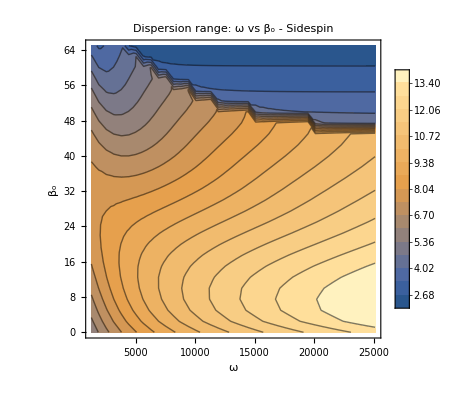

```mathematica
dispList = {};
zdispList = {};
For[o=1, o<= Length[initialOmegas], o++,
For[b=1,b<=Length[anglesBeta],b++,
AppendTo[dispList,{initialOmegas[[o]],anglesBeta[[b]]*(360/(2π)),resultsTableBetaOmega[[o,b,6]]}];
AppendTo[zdispList,{initialOmegas[[o]],anglesBeta[[b]]*(360/(2π)),resultsTableBetaOmega[[o,b,7]]}];

]
]
(*Print[dispList]*)
ListContourPlot[dispList,InterpolationOrder->1,Contours->20, 
ContourLabels->Automatic,
PlotLegends->Automatic,
FrameLabel->{"ω","β_o"},
PlotLabel->"Dispersion range: ω vs β_o - Sidespin"]
```

```mathematica
phiLow=90;
phiHi=270;
betaLow=0;
betaHi=65;
omegaLow=100;
omegaHi=4000;
angles = Range[phiLow*((2*π)/360),phiHi*((2*π)/360),2*((2*π)/360)];
anglesBeta = Range[betaLow*((2*π)/360),betaHi*((2*π)/360),5*((2*π)/360)];
initialOmegas = Range[omegaLow*2π,omegaHi*2π,100*2π];
```

```mathematica
(* 3d + color *)
$HistoryLength=10;
Clear[Subscript[x, o],Subscript[y, o],Subscript[z, o],Subscript[α, o],Subscript[ϕ, o],Subscript[vx, o],Subscript[vy, o],Subscript[vz, o],Subscript[v, o],ω]
Subscript[x, o]=0;
Subscript[y, o]=1;
Subscript[z, o]=0;
Subscript[v, o] = 10;
Subscript[α, o]=(0.1)*((2*π)/360);
Subscript[ϕ, o]=180*((2*π)/360);
Subscript[vx, o] = Subscript[v, o]*Cos[45*((2π)/360)];
Subscript[vy, o] = Subscript[v, o]*Sin[45*((2π)/360)];
Subscript[vz, o]=0; 
ω=1600;
Monitor[
resultsTablePhiBetaOmega75h10v= Table[solveEquations[Subscript[x, o],.75,Subscript[z, o],Cos[beta]*10,Sin[beta]*10,Subscript[vz, o],Subscript[α, o],phi,omega],{phi,angles},{omega,initialOmegas}, {beta,anglesBeta}],
Grid[
{{Text[Style["Phi :",Darker[Blue,0.66]]],ProgressIndicator[phi,{phiLow*((2π)/360),phiHi*((2π)/360)}],Text[Style["ϕ: ",Darker[Blue,0.66]]],phi*(360/(2π))},
{Text[Style["Omega :",Darker[Blue,0.66]]],ProgressIndicator[omega,{omegaLow*2π,omegaHi*2π}],Text[Style["ω: ",Darker[Blue,0.66]]],omega*(1/(2π))},
{Text[Style["Beta :",Darker[Blue,0.66]]],ProgressIndicator[beta,{betaLow*((2π)/360),betaHi*((2π)/360)}],Text[Style["β: ",Darker[Blue,0.66]]],beta*(360/(2π))}
},Alignment->Left,Dividers->Center]]

Monitor[
resultsTablePhiBetaOmega75h75v= Table[solveEquations[Subscript[x, o],.75,Subscript[z, o],Cos[beta]*7.5,Sin[beta]*7.5,Subscript[vz, o],Subscript[α, o],phi,omega],{phi,angles},{omega,initialOmegas}, {beta,anglesBeta}],
Grid[
{{Text[Style["Phi :",Darker[Blue,0.66]]],ProgressIndicator[phi,{phiLow*((2π)/360),phiHi*((2π)/360)}],Text[Style["ϕ: ",Darker[Blue,0.66]]],phi*(360/(2π))},
{Text[Style["Omega :",Darker[Blue,0.66]]],ProgressIndicator[omega,{omegaLow*2π,omegaHi*2π}],Text[Style["ω: ",Darker[Blue,0.66]]],omega*(1/(2π))},
{Text[Style["Beta :",Darker[Blue,0.66]]],ProgressIndicator[beta,{betaLow*((2π)/360),betaHi*((2π)/360)}],Text[Style["β: ",Darker[Blue,0.66]]],beta*(360/(2π))}
},Alignment->Left,Dividers->Center]]
Monitor[
resultsTablePhiBetaOmega75h5v= Table[solveEquations[Subscript[x, o],.75,Subscript[z, o],Cos[beta]*5,Sin[beta]*5,Subscript[vz, o],Subscript[α, o],phi,omega],{phi,angles},{omega,initialOmegas}, {beta,anglesBeta}],
Grid[
{{Text[Style["Phi :",Darker[Blue,0.66]]],ProgressIndicator[phi,{phiLow*((2π)/360),phiHi*((2π)/360)}],Text[Style["ϕ: ",Darker[Blue,0.66]]],phi*(360/(2π))},
{Text[Style["Omega :",Darker[Blue,0.66]]],ProgressIndicator[omega,{omegaLow*2π,omegaHi*2π}],Text[Style["ω: ",Darker[Blue,0.66]]],omega*(1/(2π))},
{Text[Style["Beta :",Darker[Blue,0.66]]],ProgressIndicator[beta,{betaLow*((2π)/360),betaHi*((2π)/360)}],Text[Style["β: ",Darker[Blue,0.66]]],beta*(360/(2π))}
},Alignment->Left,Dividers->Center]]


Monitor[
resultsTablePhiBetaOmega5h10v= Table[solveEquations[Subscript[x, o],.5,Subscript[z, o],Cos[beta]*10,Sin[beta]*10,Subscript[vz, o],Subscript[α, o],phi,omega],{phi,angles},{omega,initialOmegas}, {beta,anglesBeta}],
Grid[
{{Text[Style["Phi :",Darker[Blue,0.66]]],ProgressIndicator[phi,{phiLow*((2π)/360),phiHi*((2π)/360)}],Text[Style["ϕ: ",Darker[Blue,0.66]]],phi*(360/(2π))},
{Text[Style["Omega :",Darker[Blue,0.66]]],ProgressIndicator[omega,{omegaLow*2π,omegaHi*2π}],Text[Style["ω: ",Darker[Blue,0.66]]],omega*(1/(2π))},
{Text[Style["Beta :",Darker[Blue,0.66]]],ProgressIndicator[beta,{betaLow*((2π)/360),betaHi*((2π)/360)}],Text[Style["β: ",Darker[Blue,0.66]]],beta*(360/(2π))}
},Alignment->Left,Dividers->Center]]

Monitor[
resultsTablePhiBetaOmega5h75v= Table[solveEquations[Subscript[x, o],.5,Subscript[z, o],Cos[beta]*7.5,Sin[beta]*7.5,Subscript[vz, o],Subscript[α, o],phi,omega],{phi,angles},{omega,initialOmegas}, {beta,anglesBeta}],
Grid[
{{Text[Style["Phi :",Darker[Blue,0.66]]],ProgressIndicator[phi,{phiLow*((2π)/360),phiHi*((2π)/360)}],Text[Style["ϕ: ",Darker[Blue,0.66]]],phi*(360/(2π))},
{Text[Style["Omega :",Darker[Blue,0.66]]],ProgressIndicator[omega,{omegaLow*2π,omegaHi*2π}],Text[Style["ω: ",Darker[Blue,0.66]]],omega*(1/(2π))},
{Text[Style["Beta :",Darker[Blue,0.66]]],ProgressIndicator[beta,{betaLow*((2π)/360),betaHi*((2π)/360)}],Text[Style["β: ",Darker[Blue,0.66]]],beta*(360/(2π))}
},Alignment->Left,Dividers->Center]]
Monitor[
resultsTablePhiBetaOmega5h5v= Table[solveEquations[Subscript[x, o],.5,Subscript[z, o],Cos[beta]*5,Sin[beta]*5,Subscript[vz, o],Subscript[α, o],phi,omega],{phi,angles},{omega,initialOmegas}, {beta,anglesBeta}],
Grid[
{{Text[Style["Phi :",Darker[Blue,0.66]]],ProgressIndicator[phi,{phiLow*((2π)/360),phiHi*((2π)/360)}],Text[Style["ϕ: ",Darker[Blue,0.66]]],phi*(360/(2π))},
{Text[Style["Omega :",Darker[Blue,0.66]]],ProgressIndicator[omega,{omegaLow*2π,omegaHi*2π}],Text[Style["ω: ",Darker[Blue,0.66]]],omega*(1/(2π))},
{Text[Style["Beta :",Darker[Blue,0.66]]],ProgressIndicator[beta,{betaLow*((2π)/360),betaHi*((2π)/360)}],Text[Style["β: ",Darker[Blue,0.66]]],beta*(360/(2π))}
},Alignment->Left,Dividers->Center]]

Monitor[
resultsTablePhiBetaOmega25h10v= Table[solveEquations[Subscript[x, o],.25,Subscript[z, o],Cos[beta]*10,Sin[beta]*10,Subscript[vz, o],Subscript[α, o],phi,omega],{phi,angles},{omega,initialOmegas}, {beta,anglesBeta}],
Grid[
{{Text[Style["Phi :",Darker[Blue,0.66]]],ProgressIndicator[phi,{phiLow*((2π)/360),phiHi*((2π)/360)}],Text[Style["ϕ: ",Darker[Blue,0.66]]],phi*(360/(2π))},
{Text[Style["Omega :",Darker[Blue,0.66]]],ProgressIndicator[omega,{omegaLow*2π,omegaHi*2π}],Text[Style["ω: ",Darker[Blue,0.66]]],omega*(1/(2π))},
{Text[Style["Beta :",Darker[Blue,0.66]]],ProgressIndicator[beta,{betaLow*((2π)/360),betaHi*((2π)/360)}],Text[Style["β: ",Darker[Blue,0.66]]],beta*(360/(2π))}
},Alignment->Left,Dividers->Center]]

Monitor[
resultsTablePhiBetaOmega25h75v= Table[solveEquations[Subscript[x, o],.25,Subscript[z, o],Cos[beta]*7.5,Sin[beta]*7.5,Subscript[vz, o],Subscript[α, o],phi,omega],{phi,angles},{omega,initialOmegas}, {beta,anglesBeta}],
Grid[
{{Text[Style["Phi :",Darker[Blue,0.66]]],ProgressIndicator[phi,{phiLow*((2π)/360),phiHi*((2π)/360)}],Text[Style["ϕ: ",Darker[Blue,0.66]]],phi*(360/(2π))},
{Text[Style["Omega :",Darker[Blue,0.66]]],ProgressIndicator[omega,{omegaLow*2π,omegaHi*2π}],Text[Style["ω: ",Darker[Blue,0.66]]],omega*(1/(2π))},
{Text[Style["Beta :",Darker[Blue,0.66]]],ProgressIndicator[beta,{betaLow*((2π)/360),betaHi*((2π)/360)}],Text[Style["β: ",Darker[Blue,0.66]]],beta*(360/(2π))}
},Alignment->Left,Dividers->Center]]
Monitor[
resultsTablePhiBetaOmega25h5v= Table[solveEquations[Subscript[x, o],.25,Subscript[z, o],Cos[beta]*5,Sin[beta]*5,Subscript[vz, o],Subscript[α, o],phi,omega],{phi,angles},{omega,initialOmegas}, {beta,anglesBeta}],
Grid[
{{Text[Style["Phi :",Darker[Blue,0.66]]],ProgressIndicator[phi,{phiLow*((2π)/360),phiHi*((2π)/360)}],Text[Style["ϕ: ",Darker[Blue,0.66]]],phi*(360/(2π))},
{Text[Style["Omega :",Darker[Blue,0.66]]],ProgressIndicator[omega,{omegaLow*2π,omegaHi*2π}],Text[Style["ω: ",Darker[Blue,0.66]]],omega*(1/(2π))},
{Text[Style["Beta :",Darker[Blue,0.66]]],ProgressIndicator[beta,{betaLow*((2π)/360),betaHi*((2π)/360)}],Text[Style["β: ",Darker[Blue,0.66]]],beta*(360/(2π))}
},Alignment->Left,Dividers->Center]]





aggregatedData = {};
For[b=1,b<=Length[anglesBeta],b++,
For[o=1, o<= Length[initialOmegas], o++,
For[p=1,p<=Length[angles],p++,
AppendTo[aggregatedData,{angles[[p]]*(360/(2π)),anglesBeta[[b]]*(360/(2π)),initialOmegas[[o]]/(2π), 0.75, 10, resultsTablePhiBetaOmega75h10v[[p,o,b,5]],resultsTablePhiBetaOmega75h10v[[p,o,b,6]]}];
AppendTo[aggregatedData,{angles[[p]]*(360/(2π)),anglesBeta[[b]]*(360/(2π)),initialOmegas[[o]]/(2π), 0.75, 7.5, resultsTablePhiBetaOmega75h75v[[p,o,b,5]],resultsTablePhiBetaOmega75h75v[[p,o,b,6]]}];
AppendTo[aggregatedData,{angles[[p]]*(360/(2π)),anglesBeta[[b]]*(360/(2π)),initialOmegas[[o]]/(2π), 0.75, 5, resultsTablePhiBetaOmega75h5v[[p,o,b,5]],resultsTablePhiBetaOmega75h5v[[p,o,b,6]]}];

AppendTo[aggregatedData,{angles[[p]]*(360/(2π)),anglesBeta[[b]]*(360/(2π)),initialOmegas[[o]]/(2π), 0.5, 10, resultsTablePhiBetaOmega5h10v[[p,o,b,5]],resultsTablePhiBetaOmega5h10v[[p,o,b,6]]}];
AppendTo[aggregatedData,{angles[[p]]*(360/(2π)),anglesBeta[[b]]*(360/(2π)),initialOmegas[[o]]/(2π), 0.5, 7.5, resultsTablePhiBetaOmega5h75v[[p,o,b,5]],resultsTablePhiBetaOmega5h75v[[p,o,b,6]]}];
AppendTo[aggregatedData,{angles[[p]]*(360/(2π)),anglesBeta[[b]]*(360/(2π)),initialOmegas[[o]]/(2π), 0.5, 5, resultsTablePhiBetaOmega5h5v[[p,o,b,5]],resultsTablePhiBetaOmega5h5v[[p,o,b,6]]}];

AppendTo[aggregatedData,{angles[[p]]*(360/(2π)),anglesBeta[[b]]*(360/(2π)),initialOmegas[[o]]/(2π), 0.25, 10, resultsTablePhiBetaOmega25h10v[[p,o,b,5]],resultsTablePhiBetaOmega25h10v[[p,o,b,6]]}];
AppendTo[aggregatedData,{angles[[p]]*(360/(2π)),anglesBeta[[b]]*(360/(2π)),initialOmegas[[o]]/(2π), 0.25, 7.5, resultsTablePhiBetaOmega25h75v[[p,o,b,5]],resultsTablePhiBetaOmega25h75v[[p,o,b,6]]}];
AppendTo[aggregatedData,{angles[[p]]*(360/(2π)),anglesBeta[[b]]*(360/(2π)),initialOmegas[[o]]/(2π), 0.25, 5, resultsTablePhiBetaOmega25h5v[[p,o,b,5]],resultsTablePhiBetaOmega25h5v[[p,o,b,6]]}];
]
]
]
aggregatedData
```

Clear::ssym: x_o is not a symbol or a valid string pattern.

Clear::ssym: y_o is not a symbol or a valid string pattern.

Clear::ssym: z_o is not a symbol or a valid string pattern.

General::stop: Further output of Clear::ssym will be suppressed during this calculation.

Power::infy: Infinite expression 1/(√0.) encountered.

NDSolve::nlnum: The function value {-0.11832,ComplexInfinity,-4.34865,ComplexInfinity,-0.0545992,ComplexInfinity,0.276208,0.581475} is not a list of numbers with dimensions {8} at {t,x[t],x'[t],y[t],y'[t],z[t],z'[t],α[t],ϕ[t]} = {17.9447,3.44524,-0.11832,-67.1661,-4.34865,-0.621659,-0.0545992,-1.12248,4.84456}.

InterpolatingFunction::dmval: Input value {18.} lies outside the range of data in the interpolating function. Extrapolation will be used.

FindRoot::bbrac: Method -> Brent is only applicable to univariate real functions and requires two real starting values that bracket the root.

{Error:,114,65,400 π}

Power::infy: Infinite expression 1/(√0.) encountered.

NDSolve::nlnum: The function value {-0.297656,ComplexInfinity,-4.34275,ComplexInfinity,-0.163766,ComplexInfinity,0.949847,1.96348} is not a list of numbers with dimensions {8} at {t,x[t],x'[t],y[t],y'[t],z[t],z'[t],α[t],ϕ[t]} = {8.91033,2.97845,-0.297656,-28.6697,-4.34275,-0.177272,-0.163766,-1.01225,4.99125}.

InterpolatingFunction::dmval: Input value {18.} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {9.005} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

{Error:,132,65,400 π}

NDSolve::ndsz: At t == 9.52954, step size is effectively zero; singularity or stiff system suspected.

FindRoot::bbrac: Method -> Brent is only applicable to univariate real functions and requires two real starting values that bracket the root.

{Error:,150,60,600 π}

Power::infy: Infinite expression 1/(√0.) encountered.

General::stop: Further output of Power::infy will be suppressed during this calculation.

NDSolve::nlnum: The function value {-0.332243,ComplexInfinity,-4.07628,ComplexInfinity,-0.271463,ComplexInfinity,6.10111,8.24498} is not a list of numbers with dimensions {8} at {t,x[t],x'[t],y[t],y'[t],z[t],z'[t],α[t],ϕ[t]} = {8.06145,2.77504,-0.332243,-25.1001,-4.07628,0.552956,-0.271463,-0.800095,4.98075}.

General::stop: Further output of NDSolve::nlnum will be suppressed during this calculation.

{Error:,166,65,600 π}

NDSolve::mxst: Maximum number of 3498558 steps reached at the point t == 15.4196.

InterpolatingFunction::dmval: Input value {18.} lies outside the range of data in the interpolating function. Extrapolation will be used.

FindRoot::bbrac: Method -> Brent is only applicable to univariate real functions and requires two real starting values that bracket the root.

{Error:,136,60.,400 π}

Power::infy: Infinite expression 1/(√0.) encountered.

NDSolve::nlnum: The function value {0.332807,ComplexInfinity,-4.33881,ComplexInfinity,0.198392,ComplexInfinity,0.433544,0.955811} is not a list of numbers with dimensions {8} at {t,x[t],x'[t],y[t],y'[t],z[t],z'[t],α[t],ϕ[t]} = {3.5661,2.41386,0.332807,-7.81901,-4.33881,0.0694566,0.198392,-1.07865,4.68594}.

InterpolatingFunction::dmval: Input value {18.} lies outside the range of data in the interpolating function. Extrapolation will be used.

FindRoot::bbrac: Method -> Brent is only applicable to univariate real functions and requires two real starting values that bracket the root.

{Error:,138,60.,400 π}

NDSolve::ndsz: At t == 10.2985, step size is effectively zero; singularity or stiff system suspected.

InterpolatingFunction::dmval: Input value {18.} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

FindRoot::bbrac: Method -> Brent is only applicable to univariate real functions and requires two real starting values that bracket the root.

General::stop: Further output of FindRoot::bbrac will be suppressed during this calculation.

{Error:,154,55.,600 π}

Power::infy: Infinite expression 1/(√0.) encountered.

NDSolve::nlnum: The function value {-0.545412,ComplexInfinity,-3.11456,ComplexInfinity,-0.574674,ComplexInfinity,13.5513,14.1443} is not a list of numbers with dimensions {8} at {t,x[t],x'[t],y[t],y'[t],z[t],z'[t],α[t],ϕ[t]} = {3.30063,2.22783,-0.545412,-6.69719,-3.11456,0.568702,-0.574674,-0.509861,5.19284}.

{Error:,168,60.,600 π}

NDSolve::ndsz: At t == 5.66046, step size is effectively zero; singularity or stiff system suspected.

{Error:,170,55.,800 π}

Power::infy: Infinite expression 1/(√0.) encountered.

General::stop: Further output of Power::infy will be suppressed during this calculation.

NDSolve::nlnum: The function value {-0.182762,ComplexInfinity,-2.94854,ComplexInfinity,-0.33177,ComplexInfinity,11.0545,6.522} is not a list of numbers with dimensions {8} at {t,x[t],x'[t],y[t],y'[t],z[t],z'[t],α[t],ϕ[t]} = {14.1604,2.92742,-0.182762,-53.201,-2.94854,0.911513,-0.33177,-0.38239,4.91573}.

General::stop: Further output of NDSolve::nlnum will be suppressed during this calculation.

{Error:,178,55.,1000 π}

NDSolve::ndsz: At t == 13.737, step size is effectively zero; singularity or stiff system suspected.

General::stop: Further output of NDSolve::ndsz will be suppressed during this calculation.

{Error:,186,60.,1000 π}

{Error:,194,65.,1000 π}

Power::infy: Infinite expression 1/(√0.) encountered.

NDSolve::nlnum: The function value {-0.322377,ComplexInfinity,-4.3374,ComplexInfinity,-0.179467,ComplexInfinity,1.0718,2.21088} is not a list of numbers with dimensions {8} at {t,x[t],x'[t],y[t],y'[t],z[t],z'[t],α[t],ϕ[t]} = {9.82979,2.1425,-0.322377,-36.7074,-4.3374,0.130299,-0.179467,-1.00083,5.01003}.

InterpolatingFunction::dmval: Input value {18.} lies outside the range of data in the interpolating function. Extrapolation will be used.

{Error:,140,50,400 π}

NDSolve::ndsz: At t == 7.58062, step size is effectively zero; singularity or stiff system suspected.

InterpolatingFunction::dmval: Input value {18.} lies outside the range of data in the interpolating function. Extrapolation will be used.

FindRoot::bbrac: Method -> Brent is only applicable to univariate real functions and requires two real starting values that bracket the root.

{Error:,158,45,600 π}

NDSolve::ndsz: At t == 17.3141, step size is effectively zero; singularity or stiff system suspected.

InterpolatingFunction::dmval: Input value {18.} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

FindRoot::bbrac: Method -> Brent is only applicable to univariate real functions and requires two real starting values that bracket the root.

{Error:,162,40,800 π}

NDSolve::ndsz: At t == 2.56879, step size is effectively zero; singularity or stiff system suspected.

General::stop: Further output of NDSolve::ndsz will be suppressed during this calculation.

FindRoot::bbrac: Method -> Brent is only applicable to univariate real functions and requires two real starting values that bracket the root.

General::stop: Further output of FindRoot::bbrac will be suppressed during this calculation.

{Error:,170,50,600 π}

{Error:,172,45,800 π}

Power::infy: Infinite expression 1/(√0.) encountered.

NDSolve::nlnum: The function value {-0.188035,ComplexInfinity,-2.91735,ComplexInfinity,-0.356533,ComplexInfinity,10.4066,6.07271} is not a list of numbers with dimensions {8} at {t,x[t],x'[t],y[t],y'[t],z[t],z'[t],α[t],ϕ[t]} = {16.5523,2.86303,-0.188035,-65.2851,-2.91735,0.767318,-0.356533,-0.353944,4.92597}.

{Error:,172,40,1000 π}

{Error:,180,50,800 π}

Power::infy: Infinite expression 1/(√0.) encountered.

General::stop: Further output of Power::infy will be suppressed during this calculation.

NDSolve::nlnum: The function value {-0.494031,ComplexInfinity,-3.37829,ComplexInfinity,-0.491477,ComplexInfinity,13.3937,15.1308} is not a list of numbers with dimensions {8} at {t,x[t],x'[t],y[t],y'[t],z[t],z'[t],α[t],ϕ[t]} = {3.86709,1.52625,-0.494031,-11.2838,-3.37829,0.652189,-0.491477,-0.593182,5.13242}.

General::stop: Further output of NDSolve::nlnum will be suppressed during this calculation.

{Error:,188,60,600 π}

{Error:,188,55,800 π}

{Error:,196,65,600 π}

Power::infy: Infinite expression 1/(√0.) encountered.

NDSolve::nlnum: The function value {0.390608,ComplexInfinity,-4.33112,ComplexInfinity,0.254438,ComplexInfinity,0.582412,1.28678} is not a list of numbers with dimensions {8} at {t,x[t],x'[t],y[t],y'[t],z[t],z'[t],α[t],ϕ[t]} = {3.29168,3.28504,0.390608,-4.61255,-4.33112,-0.577074,0.254438,-1.05164,4.67762}.

InterpolatingFunction::dmval: Input value {18.} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {9.005} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {13.5025} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

FindRoot::brmp: The root has been bracketed as closely as possible with machine precision but the function value exceeds the absolute tolerance 1.05367×10^-8.

{Error:,112,65,400 π}

Power::infy: Infinite expression 1/(√(0.+0. ⅈ)) encountered.

NDSolve::nlnum: The function value {0.148106+0. ⅈ,ComplexInfinity,-4.32744+0. ⅈ,ComplexInfinity,0.0621929+0. ⅈ,ComplexInfinity,0.123363+0. ⅈ,0.268514+0. ⅈ} is not a list of numbers with dimensions {8} at {t,x[t],x'[t],y[t],y'[t],z[t],z'[t],α[t],ϕ[t]} = {17.5824,3.44063+0. ⅈ,0.148106+0. ⅈ,-65.844+0. ⅈ,-4.32744+0. ⅈ,-0.623427+0. ⅈ,0.0621929+0. ⅈ,-1.18759+0. ⅈ,4.70466+0. ⅈ}.

{Error:,114,65,400 π}

Power::infy: Infinite expression 1/(√0.) encountered.

General::stop: Further output of Power::infy will be suppressed during this calculation.

NDSolve::nlnum: The function value {-0.297676,ComplexInfinity,-4.34275,ComplexInfinity,-0.163778,ComplexInfinity,0.949927,1.96364} is not a list of numbers with dimensions {8} at {t,x[t],x'[t],y[t],y'[t],z[t],z'[t],α[t],ϕ[t]} = {8.91034,2.97845,-0.297676,-28.9197,-4.34275,-0.177273,-0.163778,-1.01224,4.99127}.

General::stop: Further output of NDSolve::nlnum will be suppressed during this calculation.

{Error:,132,65,400 π}

{Error:,150,60,600 π}

NDSolve::ndsz: At t == 8.06145, step size is effectively zero; singularity or stiff system suspected.

FindRoot::bbrac: Method -> Brent is only applicable to univariate real functions and requires two real starting values that bracket the root.

{Error:,166,65,600 π}

Power::infy: Infinite expression 1/(√0.) encountered.

NDSolve::nlnum: The function value {-0.127191,ComplexInfinity,-4.35011,ComplexInfinity,-0.0595949,ComplexInfinity,0.301331,0.633648} is not a list of numbers with dimensions {8} at {t,x[t],x'[t],y[t],y'[t],z[t],z'[t],α[t],ϕ[t]} = {15.4195,2.5945,-0.127191,-58.8483,-4.35011,-0.0142865,-0.0595949,-1.11503,4.85249}.

InterpolatingFunction::dmval: Input value {18.} lies outside the range of data in the interpolating function. Extrapolation will be used.

{Error:,136,60.,400 π}

Power::infy: Infinite expression 1/(√0.) encountered.

NDSolve::nlnum: The function value {0.414657,ComplexInfinity,-4.32578,ComplexInfinity,0.285364,ComplexInfinity,0.71009,1.04574} is not a list of numbers with dimensions {8} at {t,x[t],x'[t],y[t],y'[t],z[t],z'[t],α[t],ϕ[t]} = {10.18,2.86955,0.414657,-36.4214,-4.32578,0.372016,0.285364,-1.03328,4.67286}.

InterpolatingFunction::dmval: Input value {18.} lies outside the range of data in the interpolating function. Extrapolation will be used.

{Error:,154,55.,600 π}

Power::infy: Infinite expression 1/(√0.) encountered.

General::stop: Further output of Power::infy will be suppressed during this calculation.

NDSolve::nlnum: The function value {-0.545412,ComplexInfinity,-3.11456,ComplexInfinity,-0.574674,ComplexInfinity,13.5513,14.1443} is not a list of numbers with dimensions {8} at {t,x[t],x'[t],y[t],y'[t],z[t],z'[t],α[t],ϕ[t]} = {3.30063,2.22783,-0.545412,-6.94719,-3.11456,0.568702,-0.574674,-0.509861,5.19284}.

General::stop: Further output of NDSolve::nlnum will be suppressed during this calculation.

InterpolatingFunction::dmval: Input value {18.} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

FindRoot::bbrac: Method -> Brent is only applicable to univariate real functions and requires two real starting values that bracket the root.

{Error:,168,60.,600 π}

FindRoot::bbrac: Method -> Brent is only applicable to univariate real functions and requires two real starting values that bracket the root.

{Error:,170,55.,800 π}

FindRoot::bbrac: Method -> Brent is only applicable to univariate real functions and requires two real starting values that bracket the root.

General::stop: Further output of FindRoot::bbrac will be suppressed during this calculation.

{Error:,178,55.,1000 π}

NDSolve::ndsz: At t == 13.737, step size is effectively zero; singularity or stiff system suspected.

{Error:,186,60.,1000 π}

{Error:,194,65.,1000 π}

NDSolve::ndsz: At t == 9.82994, step size is effectively zero; singularity or stiff system suspected.

InterpolatingFunction::dmval: Input value {18.} lies outside the range of data in the interpolating function. Extrapolation will be used.

FindRoot::bbrac: Method -> Brent is only applicable to univariate real functions and requires two real starting values that bracket the root.

{Error:,140,50,400 π}

NDSolve::ndsz: At t == 7.58062, step size is effectively zero; singularity or stiff system suspected.

InterpolatingFunction::dmval: Input value {18.} lies outside the range of data in the interpolating function. Extrapolation will be used.

FindRoot::bbrac: Method -> Brent is only applicable to univariate real functions and requires two real starting values that bracket the root.

{Error:,158,45,600 π}

NDSolve::ndsz: At t == 17.3142, step size is effectively zero; singularity or stiff system suspected.

General::stop: Further output of NDSolve::ndsz will be suppressed during this calculation.

InterpolatingFunction::dmval: Input value {18.} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

FindRoot::bbrac: Method -> Brent is only applicable to univariate real functions and requires two real starting values that bracket the root.

General::stop: Further output of FindRoot::bbrac will be suppressed during this calculation.

{Error:,162,40,800 π}

{Error:,170,50,600 π}

Power::infy: Infinite expression 1/(√0.) encountered.

NDSolve::nlnum: The function value {-0.234806,ComplexInfinity,-3.63285,ComplexInfinity,-0.258553,ComplexInfinity,11.9082,10.8179} is not a list of numbers with dimensions {8} at {t,x[t],x'[t],y[t],y'[t],z[t],z'[t],α[t],ϕ[t]} = {14.1757,2.49064,-0.234806,-55.5237,-3.63285,0.709261,-0.258553,-0.655495,4.91472}.

{Error:,172,45,800 π}

Power::infy: Infinite expression 1/(√0.) encountered.

NDSolve::nlnum: The function value {-0.188035,ComplexInfinity,-2.91735,ComplexInfinity,-0.356532,ComplexInfinity,10.4066,6.07272} is not a list of numbers with dimensions {8} at {t,x[t],x'[t],y[t],y'[t],z[t],z'[t],α[t],ϕ[t]} = {16.5523,2.86303,-0.188035,-65.5352,-2.91735,0.767317,-0.356532,-0.353944,4.92597}.

Power::infy: Infinite expression 1/(√0.) encountered.

General::stop: Further output of Power::infy will be suppressed during this calculation.

NDSolve::nlnum: The function value {-0.188035,ComplexInfinity,-2.91735,ComplexInfinity,-0.356532,ComplexInfinity,10.4066,6.07272} is not a list of numbers with dimensions {8} at {t,x[t],x'[t],y[t],y'[t],z[t],z'[t],α[t],ϕ[t]} = {16.5523,2.86303,-0.188035,-65.5352,-2.91735,0.767317,-0.356532,-0.353944,4.92597}.

General::stop: Further output of NDSolve::nlnum will be suppressed during this calculation.

{Error:,172,40,1000 π}

{Error:,180,50,800 π}

{Error:,188,60,600 π}

{Error:,188,55,800 π}

{Error:,196,65,600 π}

Power::infy: Infinite expression 1/(√0.) encountered.

NDSolve::nlnum: The function value {0.390609,ComplexInfinity,-4.33112,ComplexInfinity,0.254439,ComplexInfinity,0.582415,1.28678} is not a list of numbers with dimensions {8} at {t,x[t],x'[t],y[t],y'[t],z[t],z'[t],α[t],ϕ[t]} = {3.29167,3.28504,0.390609,-4.8625,-4.33112,-0.577074,0.254439,-1.05163,4.67762}.

InterpolatingFunction::dmval: Input value {18.} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {9.005} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {4.5075} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

FindRoot::brmp: The root has been bracketed as closely as possible with machine precision but the function value exceeds the absolute tolerance 1.05367×10^-8.

{Error:,112,65,400 π}

Power::infy: Infinite expression 1/(√0.) encountered.

NDSolve::nlnum: The function value {-0.118509,ComplexInfinity,-4.34867,ComplexInfinity,-0.0546946,ComplexInfinity,0.276511,0.582077} is not a list of numbers with dimensions {8} at {t,x[t],x'[t],y[t],y'[t],z[t],z'[t],α[t],ϕ[t]} = {17.945,3.4452,-0.118509,-67.6674,-4.34867,-0.621676,-0.0546946,-1.12239,4.84475}.

FindRoot::bbrac: Method -> Brent is only applicable to univariate real functions and requires two real starting values that bracket the root.

{Error:,114,65,400 π}

Power::infy: Infinite expression 1/(√0.) encountered.

General::stop: Further output of Power::infy will be suppressed during this calculation.

NDSolve::nlnum: The function value {-0.297645,ComplexInfinity,-4.34276,ComplexInfinity,-0.163759,ComplexInfinity,0.949802,1.96339} is not a list of numbers with dimensions {8} at {t,x[t],x'[t],y[t],y'[t],z[t],z'[t],α[t],ϕ[t]} = {8.91033,2.97845,-0.297645,-29.1697,-4.34276,-0.177271,-0.163759,-1.01225,4.99125}.

General::stop: Further output of NDSolve::nlnum will be suppressed during this calculation.

FindRoot::bbrac: Method -> Brent is only applicable to univariate real functions and requires two real starting values that bracket the root.

{Error:,132,65,400 π}

{Error:,150,60,600 π}

FindRoot::bbrac: Method -> Brent is only applicable to univariate real functions and requires two real starting values that bracket the root.

General::stop: Further output of FindRoot::bbrac will be suppressed during this calculation.

{Error:,166,65,600 π}

NDSolve::mxst: Maximum number of 4162092 steps reached at the point t == 15.4197.

InterpolatingFunction::dmval: Input value {18.} lies outside the range of data in the interpolating function. Extrapolation will be used.

FindRoot::bbrac: Method -> Brent is only applicable to univariate real functions and requires two real starting values that bracket the root.

{Error:,136,60.,400 π}

NDSolve::ndsz: At t == 10.2985, step size is effectively zero; singularity or stiff system suspected.

InterpolatingFunction::dmval: Input value {18.} lies outside the range of data in the interpolating function. Extrapolation will be used.

FindRoot::bbrac: Method -> Brent is only applicable to univariate real functions and requires two real starting values that bracket the root.

{Error:,154,55.,600 π}

Power::infy: Infinite expression 1/(√0.) encountered.

NDSolve::nlnum: The function value {-0.545412,ComplexInfinity,-3.11456,ComplexInfinity,-0.574674,ComplexInfinity,13.5513,14.1443} is not a list of numbers with dimensions {8} at {t,x[t],x'[t],y[t],y'[t],z[t],z'[t],α[t],ϕ[t]} = {3.30063,2.22783,-0.545412,-7.19719,-3.11456,0.568702,-0.574674,-0.509861,5.19284}.

Power::infy: Infinite expression 1/(√0.) encountered.

NDSolve::nlnum: The function value {-0.545412,ComplexInfinity,-3.11456,ComplexInfinity,-0.574674,ComplexInfinity,13.5513,14.1443} is not a list of numbers with dimensions {8} at {t,x[t],x'[t],y[t],y'[t],z[t],z'[t],α[t],ϕ[t]} = {3.30063,2.22783,-0.545412,-7.19719,-3.11456,0.568702,-0.574674,-0.509861,5.19284}.

Power::infy: Infinite expression 1/(√0.) encountered.

General::stop: Further output of Power::infy will be suppressed during this calculation.

NDSolve::nlnum: The function value {-0.545412,ComplexInfinity,-3.11456,ComplexInfinity,-0.574674,ComplexInfinity,13.5513,14.1443} is not a list of numbers with dimensions {8} at {t,x[t],x'[t],y[t],y'[t],z[t],z'[t],α[t],ϕ[t]} = {3.30063,2.22783,-0.545412,-7.19719,-3.11456,0.568702,-0.574674,-0.509861,5.19284}.

General::stop: Further output of NDSolve::nlnum will be suppressed during this calculation.

NDSolve::ndsz: At t == 3.30063, step size is effectively zero; singularity or stiff system suspected.

InterpolatingFunction::dmval: Input value {18.} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

FindRoot::brmp: The root has been bracketed as closely as possible with machine precision but the function value exceeds the absolute tolerance 1.05367×10^-8.

{Error:,168,60.,600 π}

{Error:,170,55.,800 π}

FindRoot::bbrac: Method -> Brent is only applicable to univariate real functions and requires two real starting values that bracket the root.

General::stop: Further output of FindRoot::bbrac will be suppressed during this calculation.

{Error:,178,55.,1000 π}

{Error:,186,60.,1000 π}

NDSolve::ndsz: At t == 13.7593, step size is effectively zero; singularity or stiff system suspected.

General::stop: Further output of NDSolve::ndsz will be suppressed during this calculation.

{Error:,194,65.,1000 π}

Power::infy: Infinite expression 1/(√0.) encountered.

NDSolve::nlnum: The function value {-0.322379,ComplexInfinity,-4.3374,ComplexInfinity,-0.179468,ComplexInfinity,1.07181,2.2109} is not a list of numbers with dimensions {8} at {t,x[t],x'[t],y[t],y'[t],z[t],z'[t],α[t],ϕ[t]} = {9.82979,2.1425,-0.322379,-37.2074,-4.3374,0.130299,-0.179468,-1.00083,5.01003}.

InterpolatingFunction::dmval: Input value {18.} lies outside the range of data in the interpolating function. Extrapolation will be used.

FindRoot::bbrac: Method -> Brent is only applicable to univariate real functions and requires two real starting values that bracket the root.

{Error:,140,50,400 π}

NDSolve::ndsz: At t == 7.58062, step size is effectively zero; singularity or stiff system suspected.

InterpolatingFunction::dmval: Input value {18.} lies outside the range of data in the interpolating function. Extrapolation will be used.

FindRoot::bbrac: Method -> Brent is only applicable to univariate real functions and requires two real starting values that bracket the root.

{Error:,158,45,600 π}

NDSolve::ndsz: At t == 17.3142, step size is effectively zero; singularity or stiff system suspected.

InterpolatingFunction::dmval: Input value {18.} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

FindRoot::bbrac: Method -> Brent is only applicable to univariate real functions and requires two real starting values that bracket the root.

General::stop: Further output of FindRoot::bbrac will be suppressed during this calculation.

{Error:,162,40,800 π}

NDSolve::ndsz: At t == 2.56883, step size is effectively zero; singularity or stiff system suspected.

General::stop: Further output of NDSolve::ndsz will be suppressed during this calculation.

{Error:,170,50,600 π}

Power::infy: Infinite expression 1/(√0.) encountered.

NDSolve::nlnum: The function value {-0.234806,ComplexInfinity,-3.63285,ComplexInfinity,-0.258553,ComplexInfinity,11.9082,10.8179} is not a list of numbers with dimensions {8} at {t,x[t],x'[t],y[t],y'[t],z[t],z'[t],α[t],ϕ[t]} = {14.1757,2.49064,-0.234806,-55.7737,-3.63285,0.709261,-0.258553,-0.655495,4.91472}.

{Error:,172,45,800 π}

{Error:,172,40,1000 π}

{Error:,180,50,800 π}

Power::infy: Infinite expression 1/(√0.) encountered.

General::stop: Further output of Power::infy will be suppressed during this calculation.

NDSolve::nlnum: The function value {-0.494031,ComplexInfinity,-3.37829,ComplexInfinity,-0.491477,ComplexInfinity,13.3937,15.1308} is not a list of numbers with dimensions {8} at {t,x[t],x'[t],y[t],y'[t],z[t],z'[t],α[t],ϕ[t]} = {3.86709,1.52625,-0.494031,-11.7838,-3.37829,0.652189,-0.491477,-0.593182,5.13242}.

General::stop: Further output of NDSolve::nlnum will be suppressed during this calculation.

{Error:,188,60,600 π}

FindRoot::brmp: The root has been bracketed as closely as possible with machine precision but the function value exceeds the absolute tolerance 1.05367×10^-8.

{Error:,188,55,800 π}

{Error:,196,65,600 π}

```mathematica
Save["C:\\Users\\hesse\\Desktop\\F21\\Thesis\\SimData\\sd_v2.csv",aggregatedData]
```

```mathematica
Export["C:\\Users\\hesse\\Desktop\\F21\\Thesis\\SimData\\sd_v2_2.csv", aggregatedData]
```

C:\Users\hesse\Desktop\F21\Thesis\SimData\sd_v2_2.csv

```mathematica
(*1 - beta 
2 - omega
3 - phi 
4 - dep var (disp)*)

overallList1 = {};
overallList75 = {};
overallList5 = {};
dispList1 = {};
dispList5 = {};
dispList75 = {};
bestList1 = {};
bestList75 = {};
bestList5 = {};
worstList1 = {};
worstList75 = {};
worstList5 = {};
diffList1 = {};
diffList75 = {};
diffList5 = {};
For[b=1,b<=Length[anglesBeta],b++,
For[o=1, o<= Length[initialOmegas], o++,
maxrange1 = 0;
bestPhi1=0;
minrange1 = 1000;
worstPhi1=0;
maxrange75 = 0;
bestPhi75=0;
minrange75 = 1000;
worstPhi75=0;
maxrange5 = 0;
bestPhi5=0;
minrange5 = 1000;
worstPhi5=0;
For[p=1,p<=Length[angles],p++,

range1 = resultsTablePhiBetaOmega1[[p,o,b,6]];
If[range1>maxrange1,maxrange1=range1;bestPhi1=angles[[p]](360/(2π))];
If[range1<minrange1,minrange1=range1;worstPhi1=angles[[p]](360/(2π))];

range75 = resultsTablePhiBetaOmega75[[p,o,b,6]];
If[range75>maxrange75,maxrange75=range75;bestPhi75=angles[[p]](360/(2π))];
If[range1<minrange75,minrange75=range1;worstPhi75=angles[[p]](360/(2π))];

range5 = resultsTablePhiBetaOmega5[[p,o,b,6]];
If[range5>maxrange5,maxrange5=range5;bestPhi5=angles[[p]](360/(2π))];
If[range1<minrange5,minrange5=range1;worstPhi5=angles[[p]](360/(2π))];

AppendTo[dispList1,{angles[[p]]*(360/(2π)),anglesBeta[[b]]*(360/(2π)),initialOmegas[[o]]/(2π),resultsTablePhiBetaOmega1[[p,o,b,1;;6]]}];
AppendTo[dispList75,{angles[[p]]*(360/(2π)),anglesBeta[[b]]*(360/(2π)),initialOmegas[[o]]/(2π),resultsTablePhiBetaOmega75[[p,o,b,1;;6]]}];
AppendTo[dispList5,{angles[[p]]*(360/(2π)),anglesBeta[[b]]*(360/(2π)),initialOmegas[[o]]/(2π),resultsTablePhiBetaOmega5[[p,o,b,1;;6]]}];

];
AppendTo[bestList1,{anglesBeta[[b]]*(360/(2π)),initialOmegas[[o]]/(2π),bestPhi1}];
AppendTo[bestList75,{anglesBeta[[b]]*(360/(2π)),initialOmegas[[o]]/(2π),bestPhi75}];
AppendTo[bestList5,{anglesBeta[[b]]*(360/(2π)),initialOmegas[[o]]/(2π),bestPhi5}];
AppendTo[worstList1,{anglesBeta[[b]]*(360/(2π)),initialOmegas[[o]]/(2π),worstPhi1}];
AppendTo[worstList75,{anglesBeta[[b]]*(360/(2π)),initialOmegas[[o]]/(2π),worstPhi75}];
AppendTo[worstList5,{anglesBeta[[b]]*(360/(2π)),initialOmegas[[o]]/(2π),worstPhi5}];
AppendTo[diffList1,{anglesBeta[[b]]*(360/(2π)),initialOmegas[[o]]/(2π),bestPhi1-worstPhi1}];
AppendTo[diffList75,{anglesBeta[[b]]*(360/(2π)),initialOmegas[[o]]/(2π),bestPhi75-worstPhi75}];
AppendTo[diffList5,{anglesBeta[[b]]*(360/(2π)),initialOmegas[[o]]/(2π),bestPhi5-worstPhi5}];
];
];
dispList;
```

```mathematica
(*  saved calculation results*)
Save["C:\\Users\\hesse\\Desktop\\F21\\Thesis\\SimData\\bm_bestPhi_v2",{bestList1,bestList75,bestList5,worstList1,worstList75,worstList5,diffList1,diffList5,diffList75,dispList1,dispList75,dispList5}]
```

```mathematica
(* Load calculation results from file *)
Get["C:\\Users\\hesse\\Desktop\\F21\\Thesis\\SimData\\sd_bestPhi_v2"]
```

{{90.,0,200,{90.,0.1,0,400 π,0.318781,2.87951}},{92.5,0,200,{92.5,0.1,0,400 π,0.319325,2.88346}},{95.,0,200,{95.,0.1,0,400 π,0.321767,2.90308}},{97.5,0,200,{97.5,0.1,0,400 π,0.32621,2.9397}},93944,{265.,64,4000,{265.,0.1,64,8000 π,1.70019,5.29343}},{267.5,64,4000,{267.5,0.1,64,8000 π,1.69668,5.30503}},{270.,64,4000,{270.,0.1,64,8000 π,1.69581,5.31601}}}
 |  |  |  |

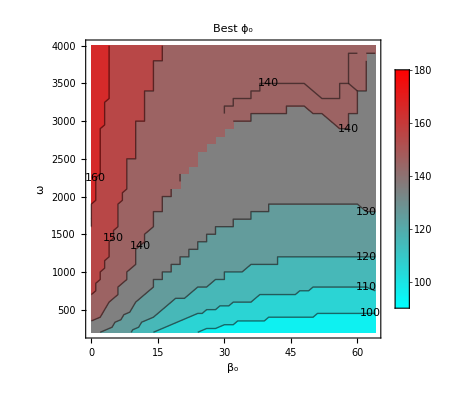

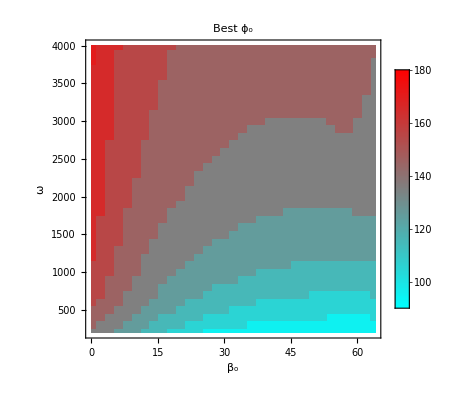

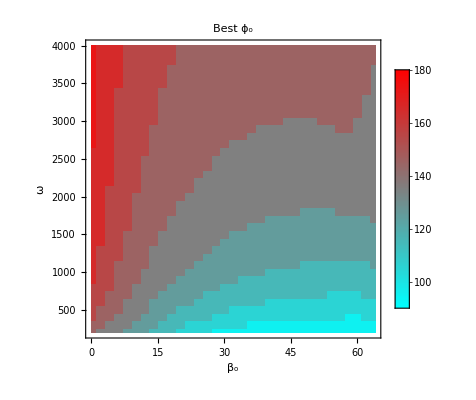

```mathematica
plotBP1=ListContourPlot[bestList1,InterpolationOrder->1, Contours->Range[90,180,10],
ColorFunction->(Blend[{{90,Cyan},{0,White},{180,Red}},#]&),
ColorFunctionScaling->False,
PlotLegends->BarLegend[{(Blend[{{90,Cyan},{0,White},{180,Red}},#]&),{90,180}}],
FrameLabel->{"β_o", "ω"},
ContourLabels->All,
GridLinesStyle->Directive[Black,Thick],
PlotLabel->"Best ϕ_o"]
Export["C:\\Users\\hesse\\Desktop\\F21\\Thesis\\figures\\Results\\functional\\seed\\sd_TEMP1.jpg",plotBP1];

plotBP75=ListContourPlot[bestList75,InterpolationOrder->0, Contours->Range[90,180,10],
ColorFunction->(Blend[{{90,Cyan},{0,White},{180,Red}},#]&),
ColorFunctionScaling->False,
PlotLegends->BarLegend[{(Blend[{{90,Cyan},{0,White},{180,Red}},#]&),{90,180}}],
FrameLabel->{"β_o", "ω"},
ContourLabels->All,
GridLinesStyle->Directive[Black,Thick],
PlotLabel->"Best ϕ_o"]
Export["C:\\Users\\hesse\\Desktop\\F21\\Thesis\\figures\\Results\\functional\\seed\\sd_TEMP75.jpg",plotBP75];

plotBP5=ListContourPlot[bestList5,InterpolationOrder->0, Contours->Range[90,180,10],
ColorFunction->(Blend[{{90,Cyan},{0,White},{180,Red}},#]&),
ColorFunctionScaling->False,
PlotLegends->BarLegend[{(Blend[{{90,Cyan},{0,White},{180,Red}},#]&),{90,180}}],
FrameLabel->{"β_o", "ω"},
ContourLabels->All,
GridLinesStyle->Directive[Black,Thick],
PlotLabel->"Best ϕ_o"]
Export["C:\\Users\\hesse\\Desktop\\F21\\Thesis\\figures\\Results\\functional\\seed\\sd_TEMP5.jpg",plotBP5];
```

```mathematica
(*ListContourPlot3D[dispList,Contours->25,ColorFunction->"TemperatureMap",AxesLabel->{"ϕ","β","ω"},
ViewPoint->{0,0,Infinity}]*)
ListSliceContourPlot3D[dispList,
{"ZStackedPlanes",3},
AxesLabel->{"ϕ_o","β_o","ω"}]
```

-Graphics3D-